#### Scott's version

```mathematica
KnotTheoryPath = "~/projects/KnotTheory/trunk/";
AppendTo[$Path, KnotTheoryPath];
<< KnotTheory`
```

Loading KnotTheory` version of November 19, 2008, 11:39:57.9761.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
KnotTheoryDirectory[]
```

/Users/scott/projects/KnotTheory/trunk/KnotTheory

```mathematica
Kh[Knot[3,1],Program->"FastKh"][q,t]
```

LinkOpen::linke: "Error 19"

JLink`InstallJava::launch: The Java runtime could not be launched.

JLink`Java::init: Java is not running. You must call InstallJava[] to start the Java runtime.

JLink`KeepJavaObject::obj: At least one argument to KeepJavaObject was not a valid Java object.

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

LinkOpen::linke: "Error 19"

JLink`InstallJava::launch: The Java runtime could not be launched.

JLink`Java::init: Java is not running. You must call InstallJava[] to start the Java runtime.

General::stop: Further output of JLink`Java :: "init" will be suppressed during this calculation.

JLink`KeepJavaObject::obj: At least one argument to KeepJavaObject was not a valid Java object.

KnotTheory::credits: "The Khovanov homology program FastKh was written by Dror Bar-Natan."

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
Kh[Knot[3,1],Program->"JavaKh-v1"][q,t]
```

KnotTheory::credits: "The Khovanov homology program JavaKh-v1 was written by Jeremy Green in the summer of 2005 at the University of Toronto."

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
Kh[Knot[3,1],Program->"JavaKh-v2"][q,t]
```

KnotTheory::credits: "The Khovanov homology program JavaKh-v2 is an update of Jeremy Green's program JavaKh-v1, written by Scott Morrison in 2008 at Microsoft Station Q."

1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)

```mathematica
With[{K=Knot[3,1],program="JavaKh-v1"},Kh[K,Program->program][q,t]-Kh[K,Program->program,Modulus->2][q,t]]
```

-1/(q^7 t^3)-1/(q^7 t^2)

```mathematica
With[{K=Knot[3,1],program="JavaKh-v2"},Kh[K,Program->program][q,t]-Kh[K,Program->program,Modulus->2][q,t]]
```

-1/(q^7 t^3)-1/(q^7 t^2)

```mathematica
Clear[BenchmarkData]
```

```mathematica
BenchmarkData[tag_String]:={}
```

```mathematica
BenchmarkData[tag_String,n_]:=Cases[BenchmarkData[tag],{_,n,___}]
```

```mathematica
KnotWidth[K_]:=First[BR[K]]
KnotLength[K_]:=Length[BR[K]⟦2⟧]
```

```mathematica
echo[x_]:=(Print[x];x)
```

```mathematica
Off[Unset::norep]
```

```mathematica
Off[Unset::write]
```

```mathematica
Clear[benchmark]
```

```mathematica
benchmark[tag_,invariantFunction_,K_]:=Module[{data},
If[MemberQ[BenchmarkData[tag],{K,___}],Return[]];
data={K,KnotWidth[K],KnotLength[K],Sequence@@(AbsoluteTiming[invariantFunction[BR[K]]]/.Second->1)};
invariantFunction[K]=.;
If[data⟦4⟧>0.5,
Print[data];
AppendTo[BenchmarkData[tag],data];
];
];
```

```mathematica
benchmark[tag_,invariantFunction_,knots_List]:=(benchmark[tag,invariantFunction,#]&/@knots;)
```

```mathematica
benchmark["FastKh",Kh[#,Program->"FastKh","chaff"->Random[]][q,t]&,Take[AllKnots[{11,11}],-10]]
```

KnotTheory::loading: Loading precomputed data in "DTCode4KnotsTo11`".

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

{Knot[11,NonAlternating,176],4,11,10.48699,2/q^3+4/q+1/(q^19 t^8)+2/(q^17 t^7)+1/(q^15 t^7)+4/(q^15 t^6)+2/(q^13 t^6)+5/(q^13 t^5)+4/(q^11 t^5)+5/(q^11 t^4)+5/(q^9 t^4)+6/(q^9 t^3)+5/(q^7 t^3)+4/(q^7 t^2)+6/(q^5 t^2)+3/(q^5 t)+4/(q^3 t)+q t}

{Knot[11,NonAlternating,177],4,11,5.671079,8 q+7 q^3+1/(q^7 t^4)+3/(q^5 t^3)+1/(q^3 t^3)+5/(q^3 t^2)+3/(q t^2)+6/(q t)+(5 q)/t+7 q^3 t+7 q^5 t+6 q^5 t^2+7 q^7 t^2+4 q^7 t^3+6 q^9 t^3+2 q^9 t^4+4 q^11 t^4+2 q^13 t^5}

{Knot[11,NonAlternating,178],4,11,12.45317,5 q+3 q^3+2/(q t)+7 q^3 t+4 q^5 t+8 q^5 t^2+7 q^7 t^2+8 q^7 t^3+8 q^9 t^3+8 q^9 t^4+8 q^11 t^4+5 q^11 t^5+8 q^13 t^5+4 q^13 t^6+5 q^15 t^6+q^15 t^7+4 q^17 t^7+q^19 t^8}

$Aborted

```mathematica
Khv1=Function[{K},Kh[K,Program->"JavaKh-v1","chaff"->Random[]][q,t]];
Khv2=Function[{K},Kh[K,Program->"JavaKh-v2","chaff"->Random[]][q,t]];
```

```mathematica
KhU=Function[{K},UniversalKh[PD[K]]];
```

```mathematica
benchmarkComparision:=Show[Plot[x,{x,0,100}],ListPlot[Cases[Flatten[BenchmarkData["JavaKh-v1"]/.{K_,w_,l_,T1_,Except[$Failed[q,t]]}:>Cases[BenchmarkData["JavaKh-v2"],{K,w,l,T2_,Except[$Failed[q,t]]}:>{T1,T2}],1],{_,_}]],AspectRatio->1,PlotRange->All]
```

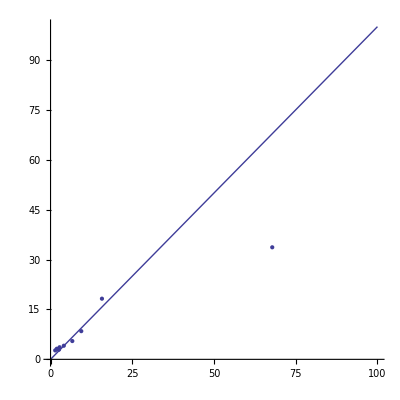

```mathematica
benchmarkComparision
```

```mathematica
Cases[Flatten[BenchmarkData["UniversalKh"]/.{K_,w_,l_,T1_,Except[$Failed[q,t]]}:>Cases[BenchmarkData["JavaKh-v2"],{K,w,l,T2_,Except[$Failed[q,t]]}:>{T1,T2}],1],{_,_}]
```

{{10.48966,6.6181},{34.33456,5.545078},{198.03188,5.731359},{12.33335,5.609656},{11.49178,6.130841},{19.39495,7.662614},{47.122912,12.51752},{8.786689,4.790217},{17.37875,5.88386}}

```mathematica
%/.{a_,b_}:>a/b
```

{1.584996,6.191898,34.55234,2.198592,1.874421,2.531114,3.764556,1.8343,2.95363}

```mathematica
benchmarkComparision2:=Show[Plot[x,{x,0,100}],ListPlot[Cases[Flatten[BenchmarkData["UniversalKh"]/.{K_,w_,l_,T1_,Except[$Failed[q,t]]}:>Cases[BenchmarkData["JavaKh-v2"],{K,w,l,T2_,Except[$Failed[q,t]]}:>{T1,T2}],1],{_,_}]],AspectRatio->1,PlotRange->All]
```

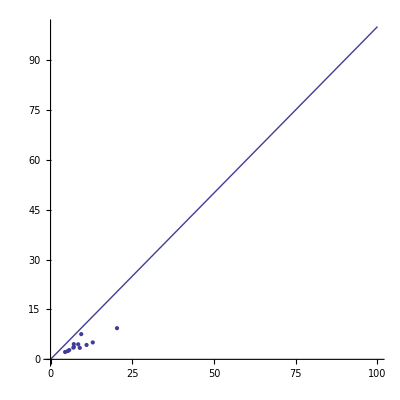

```mathematica
benchmarkComparision2
```

```mathematica
SetDirectory[ToFileName[ToFileName[KnotTheoryDirectory[],".."],"testing"]]
```

/Users/scott/projects/KnotTheory/trunk/testing

```mathematica
FileNames["*.m"]
```

{benchmarkdata.m}

```mathematica
<<benchmarkdata.m;
```

```mathematica
Save["benchmarkdata.m",BenchmarkData]
```

{Knot[15,Alternating,40117],4,15,5.67663,33/q^3+35/q+1/(q^19 t^8)+3/(q^17 t^7)+1/(q^15 t^7)+7/(q^15 t^6)+3/(q^13 t^6)+13/(q^13 t^5)+7/(q^11 t^5)+20/(q^11 t^4)+13/(q^9 t^4)+27/(q^9 t^3)+20/(q^7 t^3)+32/(q^7 t^2)+27/(q^5 t^2)+34/(q^5 t)+32/(q^3 t)+(28 t)/q+32 q t+21 q t^2+28 q^3 t^2+14 q^3 t^3+21 q^5 t^3+8 q^5 t^4+14 q^7 t^4+4 q^7 t^5+8 q^9 t^5+q^9 t^6+4 q^11 t^6+q^13 t^7}

{Knot[15,Alternating,40117],4,15,5.690756,33/q^3+35/q+1/(q^19 t^8)+3/(q^17 t^7)+1/(q^15 t^7)+7/(q^15 t^6)+3/(q^13 t^6)+13/(q^13 t^5)+7/(q^11 t^5)+20/(q^11 t^4)+13/(q^9 t^4)+27/(q^9 t^3)+20/(q^7 t^3)+32/(q^7 t^2)+27/(q^5 t^2)+34/(q^5 t)+32/(q^3 t)+(28 t)/q+32 q t+21 q t^2+28 q^3 t^2+14 q^3 t^3+21 q^5 t^3+8 q^5 t^4+14 q^7 t^4+4 q^7 t^5+8 q^9 t^5+q^9 t^6+4 q^11 t^6+q^13 t^7}

{Knot[15,Alternating,40117],4,15,14.78563,KhE/q^2+(34 KhC[1])/q^2+KhC[1]/(q^16 t^7)+(3 KhC[1])/(q^14 t^6)+(7 KhC[1])/(q^12 t^5)+(13 KhC[1])/(q^10 t^4)+(20 KhC[1])/(q^8 t^3)+(27 KhC[1])/(q^6 t^2)+(32 KhC[1])/(q^4 t)+32 t KhC[1]+28 q^2 t^2 KhC[1]+21 q^4 t^3 KhC[1]+14 q^6 t^4 KhC[1]+8 q^8 t^5 KhC[1]+4 q^10 t^6 KhC[1]+q^12 t^7 KhC[1]}

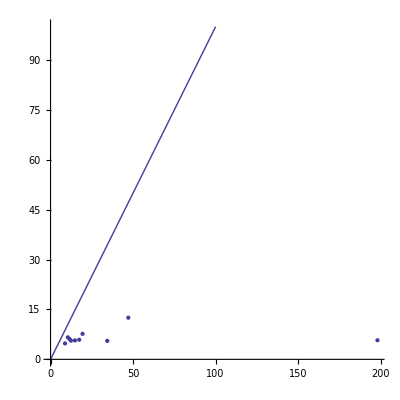

{Knot[15,NonAlternating,112333],6,25,7.694977,7/q^5+13/q^3+1/(q^25 t^10)+2/(q^23 t^9)+1/(q^21 t^9)+6/(q^21 t^8)+2/(q^19 t^8)+10/(q^19 t^7)+6/(q^17 t^7)+15/(q^17 t^6)+10/(q^15 t^6)+19/(q^15 t^5)+15/(q^13 t^5)+20/(q^13 t^4)+19/(q^11 t^4)+20/(q^11 t^3)+20/(q^9 t^3)+15/(q^9 t^2)+20/(q^7 t^2)+12/(q^7 t)+15/(q^5 t)+(3 t)/q^3+(6 t)/q+t^2/q+3 q t^2+q^3 t^3}

{Knot[15,NonAlternating,112333],6,25,7.296688,7/q^5+13/q^3+1/(q^25 t^10)+2/(q^23 t^9)+1/(q^21 t^9)+6/(q^21 t^8)+2/(q^19 t^8)+10/(q^19 t^7)+6/(q^17 t^7)+15/(q^17 t^6)+10/(q^15 t^6)+19/(q^15 t^5)+15/(q^13 t^5)+20/(q^13 t^4)+19/(q^11 t^4)+20/(q^11 t^3)+20/(q^9 t^3)+15/(q^9 t^2)+20/(q^7 t^2)+12/(q^7 t)+15/(q^5 t)+(3 t)/q^3+(6 t)/q+t^2/q+3 q t^2+q^3 t^3}

{Knot[15,NonAlternating,112333],6,25,39.876647,KhE/q^4+(12 KhC[1])/q^4+KhC[1]/(q^22 t^9)+(2 KhC[1])/(q^20 t^8)+(6 KhC[1])/(q^18 t^7)+(10 KhC[1])/(q^16 t^6)+(15 KhC[1])/(q^14 t^5)+(19 KhC[1])/(q^12 t^4)+(20 KhC[1])/(q^10 t^3)+(20 KhC[1])/(q^8 t^2)+(15 KhC[1])/(q^6 t)+(6 t KhC[1])/q^2+3 t^2 KhC[1]+q^2 t^3 KhC[1]}

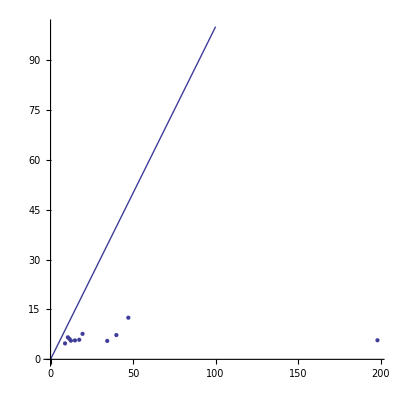

{Knot[15,NonAlternating,63220],6,25,6.182779,21 q+18 q^3+1/(q^9 t^5)+3/(q^7 t^4)+1/(q^5 t^4)+7/(q^5 t^3)+3/(q^3 t^3)+11/(q^3 t^2)+7/(q t^2)+17/(q t)+(11 q)/t+23 q^3 t+20 q^5 t+22 q^5 t^2+23 q^7 t^2+17 q^7 t^3+22 q^9 t^3+14 q^9 t^4+17 q^11 t^4+7 q^11 t^5+14 q^13 t^5+4 q^13 t^6+7 q^15 t^6+q^15 t^7+4 q^17 t^7+q^19 t^8}

{Knot[15,NonAlternating,63220],6,25,4.459862,21 q+18 q^3+1/(q^9 t^5)+3/(q^7 t^4)+1/(q^5 t^4)+7/(q^5 t^3)+3/(q^3 t^3)+11/(q^3 t^2)+7/(q t^2)+17/(q t)+(11 q)/t+23 q^3 t+20 q^5 t+22 q^5 t^2+23 q^7 t^2+17 q^7 t^3+22 q^9 t^3+14 q^9 t^4+17 q^11 t^4+7 q^11 t^5+14 q^13 t^5+4 q^13 t^6+7 q^15 t^6+q^15 t^7+4 q^17 t^7+q^19 t^8}

{Knot[15,NonAlternating,63220],6,25,11.87143,KhE q^2+17 q^2 KhC[1]+KhC[1]/(q^6 t^4)+(3 KhC[1])/(q^4 t^3)+(7 KhC[1])/(q^2 t^2)+(11 KhC[1])/t+20 q^4 t KhC[1]+23 q^6 t^2 KhC[1]+22 q^8 t^3 KhC[1]+17 q^10 t^4 KhC[1]+14 q^12 t^5 KhC[1]+7 q^14 t^6 KhC[1]+4 q^16 t^7 KhC[1]+q^18 t^8 KhC[1]}

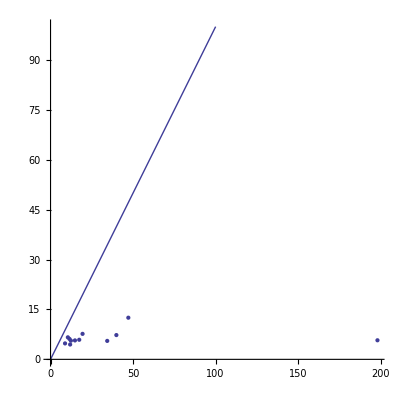

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.LCCC.<init>(LCCC.java:19)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:152)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1176)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1092)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.Cap.compose2(Cap.java:143)
	at org.katlas.JavaKh.Cap$ComposeOutput.<init>(Cap.java:281)
	at org.katlas.JavaKh.Cap.compose(Cap.java:98)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:723)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:136)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1857)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1713)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.MutableBigInteger.<init>(MutableBigInteger.java:99)
	at java.math.BigInteger.gcd(BigInteger.java:1390)
	at org.katlas.JavaKh.Rational.<init>(Rational.java:13)
	at org.katlas.JavaKh.Rational.multiply(Rational.java:28)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:143)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.BigInteger.trustedStripLeadingZeroInts(BigInteger.java:2840)
	at java.math.BigInteger.multiply(BigInteger.java:1167)
	at org.katlas.JavaKh.Rational.multiply(Rational.java:28)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:143)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:514)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.BigInteger.multiply(BigInteger.java:1168)
	at org.katlas.JavaKh.Rational.multiply(Rational.java:28)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:143)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:736)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:136)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1857)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1715)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordism$ComposeOutput.get(CannedCobordism.java:1334)
	at org.katlas.JavaKh.CannedCobordism.compose(CannedCobordism.java:401)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:142)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordism.compose(CannedCobordism.java:749)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:159)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1176)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1094)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.MutableBigInteger.<init>(MutableBigInteger.java:62)
	at java.math.MutableBigInteger.hybridGCD(MutableBigInteger.java:977)
	at java.math.BigInteger.gcd(BigInteger.java:1393)
	at org.katlas.JavaKh.algebra.rings.Rational.<init>(Rational.java:21)
	at org.katlas.JavaKh.algebra.rings.Rational.multiply(Rational.java:35)
	at org.katlas.JavaKh.algebra.rings.Rational.multiply(Rational.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.multiply(LinearComboMap.java:126)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.multiply(LinearComboMap.java:1)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1862)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1715)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordism.compose(CannedCobordism.java:749)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:159)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1176)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1092)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.Cap.compose2(Cap.java:134)
	at org.katlas.JavaKh.Cap$ComposeOutput.<init>(Cap.java:281)
	at org.katlas.JavaKh.Cap.compose(Cap.java:98)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:723)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:136)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1857)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1713)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordism$ComposeOutput.get(CannedCobordism.java:1334)
	at org.katlas.JavaKh.CannedCobordism.compose(CannedCobordism.java:401)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:142)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.MutableBigInteger.<init>(MutableBigInteger.java:62)
	at java.math.MutableBigInteger.hybridGCD(MutableBigInteger.java:978)
	at java.math.BigInteger.gcd(BigInteger.java:1393)
	at org.katlas.JavaKh.algebra.rings.Rational.<init>(Rational.java:21)
	at org.katlas.JavaKh.algebra.rings.Rational.multiply(Rational.java:35)
	at org.katlas.JavaKh.algebra.rings.Rational.multiply(Rational.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:143)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:168)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:1)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:712)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:513)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1732)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.MutableBigInteger.<init>(MutableBigInteger.java:99)
	at java.math.BigInteger.gcd(BigInteger.java:1391)
	at org.katlas.JavaKh.Rational.<init>(Rational.java:13)
	at org.katlas.JavaKh.Rational.multiply(Rational.java:28)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:143)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordismImpl.composeWithoutCache(CannedCobordismImpl.java:355)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:341)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:142)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:168)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:1)
	at org.katlas.JavaKh.CobMatrix.compose(CobMatrix.java:190)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1346)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1066)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1732)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at java.math.BigInteger.trustedStripLeadingZeroInts(BigInteger.java:2840)
	at java.math.BigInteger.multiply(BigInteger.java:1167)
	at org.katlas.JavaKh.Rational.multiply(Rational.java:28)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:143)
	at org.katlas.JavaKh.Komplex.deLoop(Komplex.java:514)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:437)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1110)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordismImpl.reverseMaps(CannedCobordismImpl.java:163)
	at org.katlas.JavaKh.CannedCobordismImpl.composeWithoutCache(CannedCobordismImpl.java:555)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:341)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:142)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:168)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:1)
	at org.katlas.JavaKh.CobMatrix.compose(CobMatrix.java:190)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1346)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1066)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:525)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1732)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:114)

{Knot[15,Alternating,84498],8,39,56.526882,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,84498],8,39,195.6047,$Failed[q,t]}

{Knot[15,Alternating,84498],8,39,141.20195,KhE q^8+3 q^12 t^2 KhC[1]+5 q^14 t^3 KhC[1]+10 q^16 t^4 KhC[1]+15 q^18 t^5 KhC[1]+20 q^20 t^6 KhC[1]+25 q^22 t^7 KhC[1]+25 q^24 t^8 KhC[1]+25 q^26 t^9 KhC[1]+20 q^28 t^10 KhC[1]+16 q^30 t^11 KhC[1]+9 q^32 t^12 KhC[1]+6 q^34 t^13 KhC[1]+2 q^36 t^14 KhC[1]+q^38 t^15 KhC[1]}

-Graphics-

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,143071],8,37,145.77674,$Failed[q,t]}

{Knot[15,NonAlternating,143071],8,37,182.97486,15 q+9 q^3+1/(q^5 t^3)+4/(q^3 t^2)+1/(q t^2)+8/(q t)+(4 q)/t+20 q^3 t+14 q^5 t+22 q^5 t^2+20 q^7 t^2+22 q^7 t^3+22 q^9 t^3+20 q^9 t^4+22 q^11 t^4+14 q^11 t^5+20 q^13 t^5+9 q^13 t^6+14 q^15 t^6+4 q^15 t^7+9 q^17 t^7+q^17 t^8+4 q^19 t^8+q^21 t^9}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

{Knot[15,NonAlternating,143071],8,37,202.20837,KnotTheory`UniversalKh`Private`DecomposeComplex[KnotTheory`UniversalKh`Private`GradingsList[$Failed],KnotTheory`UniversalKh`Private`Matrices[$Failed]]}

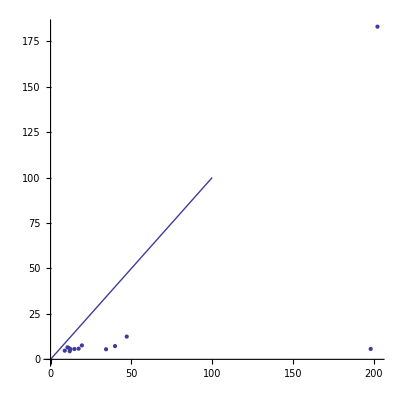

{Knot[15,Alternating,59227],6,23,13.06563,76/q+75 q+1/(q^15 t^7)+6/(q^13 t^6)+1/(q^11 t^6)+16/(q^11 t^5)+6/(q^9 t^5)+31/(q^9 t^4)+16/(q^7 t^4)+48/(q^7 t^3)+31/(q^5 t^3)+64/(q^5 t^2)+48/(q^3 t^2)+74/(q^3 t)+64/(q t)+69 q t+75 q^3 t+54 q^3 t^2+69 q^5 t^2+37 q^5 t^3+54 q^7 t^3+22 q^7 t^4+37 q^9 t^4+10 q^9 t^5+22 q^11 t^5+4 q^11 t^6+10 q^13 t^6+q^13 t^7+4 q^15 t^7+q^17 t^8}

{Knot[15,Alternating,59227],6,23,5.405484,76/q+75 q+1/(q^15 t^7)+6/(q^13 t^6)+1/(q^11 t^6)+16/(q^11 t^5)+6/(q^9 t^5)+31/(q^9 t^4)+16/(q^7 t^4)+48/(q^7 t^3)+31/(q^5 t^3)+64/(q^5 t^2)+48/(q^3 t^2)+74/(q^3 t)+64/(q t)+69 q t+75 q^3 t+54 q^3 t^2+69 q^5 t^2+37 q^5 t^3+54 q^7 t^3+22 q^7 t^4+37 q^9 t^4+10 q^9 t^5+22 q^11 t^5+4 q^11 t^6+10 q^13 t^6+q^13 t^7+4 q^15 t^7+q^17 t^8}

{Knot[15,Alternating,59227],6,23,61.422115,KhE+74 KhC[1]+KhC[1]/(q^12 t^6)+(6 KhC[1])/(q^10 t^5)+(16 KhC[1])/(q^8 t^4)+(31 KhC[1])/(q^6 t^3)+(48 KhC[1])/(q^4 t^2)+(64 KhC[1])/(q^2 t)+75 q^2 t KhC[1]+69 q^4 t^2 KhC[1]+54 q^6 t^3 KhC[1]+37 q^8 t^4 KhC[1]+22 q^10 t^5 KhC[1]+10 q^12 t^6 KhC[1]+4 q^14 t^7 KhC[1]+q^16 t^8 KhC[1]}

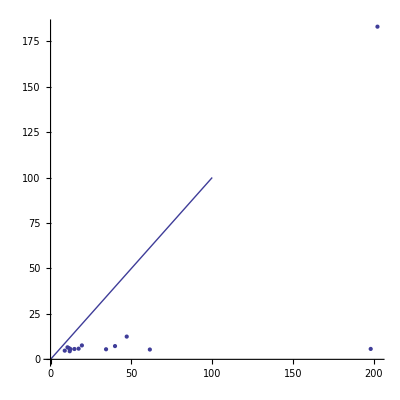

{Knot[15,NonAlternating,129801],6,23,9.50951,21 q+19 q^3+3/(q^7 t^4)+7/(q^5 t^3)+3/(q^3 t^3)+13/(q^3 t^2)+7/(q t^2)+18/(q t)+(13 q)/t+22 q^3 t+20 q^5 t+19 q^5 t^2+22 q^7 t^2+14 q^7 t^3+19 q^9 t^3+9 q^9 t^4+14 q^11 t^4+3 q^11 t^5+9 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,129801],6,23,5.901609,21 q+19 q^3+3/(q^7 t^4)+7/(q^5 t^3)+3/(q^3 t^3)+13/(q^3 t^2)+7/(q t^2)+18/(q t)+(13 q)/t+22 q^3 t+20 q^5 t+19 q^5 t^2+22 q^7 t^2+14 q^7 t^3+19 q^9 t^3+9 q^9 t^4+14 q^11 t^4+3 q^11 t^5+9 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,129801],6,23,18.89221,KhE q^2+18 q^2 KhC[1]+(3 KhC[1])/(q^4 t^3)+(7 KhC[1])/(q^2 t^2)+(13 KhC[1])/t+20 q^4 t KhC[1]+22 q^6 t^2 KhC[1]+19 q^8 t^3 KhC[1]+14 q^10 t^4 KhC[1]+9 q^12 t^5 KhC[1]+3 q^14 t^6 KhC[1]+q^16 t^7 KhC[1]}

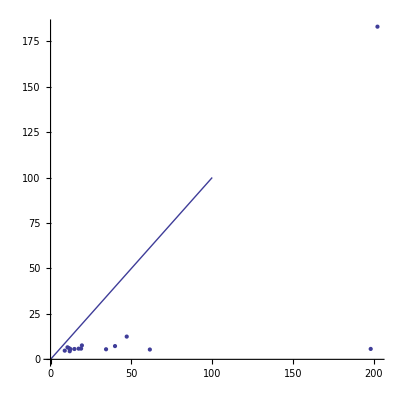

{Knot[15,NonAlternating,155156],6,23,9.327513,18/q^5+31/q^3+1/(q^25 t^10)+5/(q^23 t^9)+1/(q^21 t^9)+12/(q^21 t^8)+5/(q^19 t^8)+23/(q^19 t^7)+12/(q^17 t^7)+35/(q^17 t^6)+23/(q^15 t^6)+45/(q^15 t^5)+35/(q^13 t^5)+50/(q^13 t^4)+45/(q^11 t^4)+48/(q^11 t^3)+50/(q^9 t^3)+41/(q^9 t^2)+48/(q^7 t^2)+30/(q^7 t)+41/(q^5 t)+(9 t)/q^3+(17 t)/q+(2 t^2)/q+9 q t^2+2 q^3 t^3}

{Knot[15,NonAlternating,155156],6,23,5.943537,18/q^5+31/q^3+1/(q^25 t^10)+5/(q^23 t^9)+1/(q^21 t^9)+12/(q^21 t^8)+5/(q^19 t^8)+23/(q^19 t^7)+12/(q^17 t^7)+35/(q^17 t^6)+23/(q^15 t^6)+45/(q^15 t^5)+35/(q^13 t^5)+50/(q^13 t^4)+45/(q^11 t^4)+48/(q^11 t^3)+50/(q^9 t^3)+41/(q^9 t^2)+48/(q^7 t^2)+30/(q^7 t)+41/(q^5 t)+(9 t)/q^3+(17 t)/q+(2 t^2)/q+9 q t^2+2 q^3 t^3}

{Knot[15,NonAlternating,155156],6,23,32.59085,KhE/q^4+(30 KhC[1])/q^4+KhC[1]/(q^22 t^9)+(5 KhC[1])/(q^20 t^8)+(12 KhC[1])/(q^18 t^7)+(23 KhC[1])/(q^16 t^6)+(35 KhC[1])/(q^14 t^5)+(45 KhC[1])/(q^12 t^4)+(50 KhC[1])/(q^10 t^3)+(48 KhC[1])/(q^8 t^2)+(41 KhC[1])/(q^6 t)+(17 t KhC[1])/q^2+9 t^2 KhC[1]+2 q^2 t^3 KhC[1]}

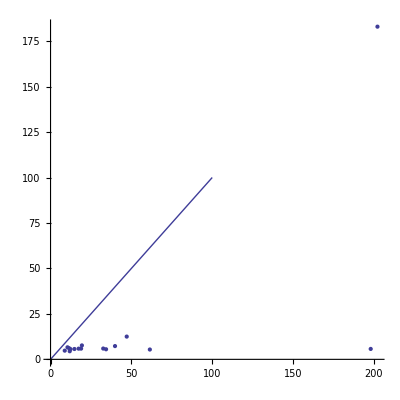

{Knot[15,NonAlternating,11941],6,23,4.339319,q^5+q^7+q^7 t+2 q^9 t^2+q^11 t^2+q^11 t^3+2 q^13 t^3+q^11 t^4+3 q^13 t^4+q^15 t^4+q^13 t^5+2 q^15 t^5+3 q^17 t^5+2 q^15 t^6+2 q^17 t^6+q^19 t^6+2 q^17 t^7+3 q^19 t^7+q^21 t^7+3 q^19 t^8+2 q^21 t^8+q^23 t^8+3 q^21 t^9+3 q^23 t^9+2 q^23 t^10+3 q^25 t^10+2 q^25 t^11+2 q^27 t^11+q^27 t^12+2 q^29 t^12+q^31 t^13}

{Knot[15,NonAlternating,11941],6,23,4.085083,q^5+q^7+q^7 t+2 q^9 t^2+q^11 t^2+q^11 t^3+2 q^13 t^3+q^11 t^4+3 q^13 t^4+q^15 t^4+q^13 t^5+2 q^15 t^5+3 q^17 t^5+2 q^15 t^6+2 q^17 t^6+q^19 t^6+2 q^17 t^7+3 q^19 t^7+q^21 t^7+3 q^19 t^8+2 q^21 t^8+q^23 t^8+3 q^21 t^9+3 q^23 t^9+2 q^23 t^10+3 q^25 t^10+2 q^25 t^11+2 q^27 t^11+q^27 t^12+2 q^29 t^12+q^31 t^13}

{Knot[15,NonAlternating,11941],6,23,10.57619,KhE q^6+q^10 t^2 KhC[1]+2 q^12 t^3 KhC[1]+q^14 t^4 KhC[1]+2 q^16 t^5 KhC[1]+q^16 t^6 KhC[1]+q^18 t^6 KhC[1]+2 q^18 t^7 KhC[1]+q^20 t^7 KhC[1]+2 q^20 t^8 KhC[1]+q^22 t^8 KhC[1]+3 q^22 t^9 KhC[1]+3 q^24 t^10 KhC[1]+2 q^26 t^11 KhC[1]+2 q^28 t^12 KhC[1]+q^30 t^13 KhC[1]+q^16 t^5 KhC[2]}

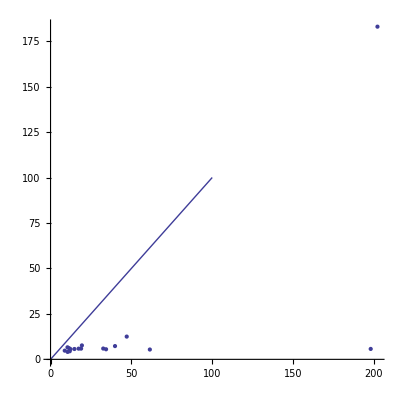

{Knot[15,NonAlternating,126081],4,15,3.37167,6 q^3+3 q^5+1/(q t^2)+(2 q)/t+q^3/t+10 q^5 t+5 q^7 t+14 q^7 t^2+10 q^9 t^2+18 q^9 t^3+14 q^11 t^3+20 q^11 t^4+18 q^13 t^4+18 q^13 t^5+20 q^15 t^5+16 q^15 t^6+18 q^17 t^6+11 q^17 t^7+16 q^19 t^7+7 q^19 t^8+11 q^21 t^8+3 q^21 t^9+7 q^23 t^9+q^23 t^10+3 q^25 t^10+q^27 t^11}

{Knot[15,NonAlternating,126081],4,15,4.260404,6 q^3+3 q^5+1/(q t^2)+(2 q)/t+q^3/t+10 q^5 t+5 q^7 t+14 q^7 t^2+10 q^9 t^2+18 q^9 t^3+14 q^11 t^3+20 q^11 t^4+18 q^13 t^4+18 q^13 t^5+20 q^15 t^5+16 q^15 t^6+18 q^17 t^6+11 q^17 t^7+16 q^19 t^7+7 q^19 t^8+11 q^21 t^8+3 q^21 t^9+7 q^23 t^9+q^23 t^10+3 q^25 t^10+q^27 t^11}

{Knot[15,NonAlternating,126081],4,15,9.882056,KhE q^4+2 q^4 KhC[1]+(q^2 KhC[1])/t+5 q^6 t KhC[1]+10 q^8 t^2 KhC[1]+14 q^10 t^3 KhC[1]+18 q^12 t^4 KhC[1]+20 q^14 t^5 KhC[1]+18 q^16 t^6 KhC[1]+16 q^18 t^7 KhC[1]+11 q^20 t^8 KhC[1]+7 q^22 t^9 KhC[1]+3 q^24 t^10 KhC[1]+q^26 t^11 KhC[1]}

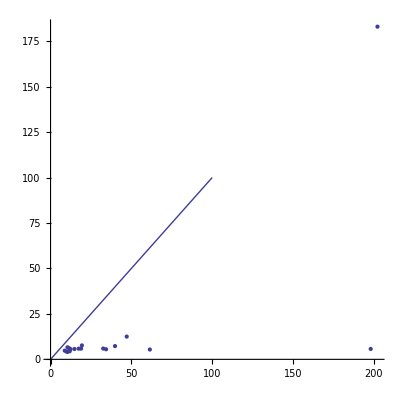

{Knot[15,Alternating,7755],6,23,12.76522,66/q+72 q+1/(q^17 t^8)+5/(q^15 t^7)+1/(q^13 t^7)+14/(q^13 t^6)+5/(q^11 t^6)+28/(q^11 t^5)+14/(q^9 t^5)+44/(q^9 t^4)+28/(q^7 t^4)+59/(q^7 t^3)+44/(q^5 t^3)+69/(q^5 t^2)+59/(q^3 t^2)+71/(q^3 t)+69/(q t)+52 q t+65 q^3 t+36 q^3 t^2+52 q^5 t^2+21 q^5 t^3+36 q^7 t^3+10 q^7 t^4+21 q^9 t^4+4 q^9 t^5+10 q^11 t^5+q^11 t^6+4 q^13 t^6+q^15 t^7}

{Knot[15,Alternating,7755],6,23,8.162477,66/q+72 q+1/(q^17 t^8)+5/(q^15 t^7)+1/(q^13 t^7)+14/(q^13 t^6)+5/(q^11 t^6)+28/(q^11 t^5)+14/(q^9 t^5)+44/(q^9 t^4)+28/(q^7 t^4)+59/(q^7 t^3)+44/(q^5 t^3)+69/(q^5 t^2)+59/(q^3 t^2)+71/(q^3 t)+69/(q t)+52 q t+65 q^3 t+36 q^3 t^2+52 q^5 t^2+21 q^5 t^3+36 q^7 t^3+10 q^7 t^4+21 q^9 t^4+4 q^9 t^5+10 q^11 t^5+q^11 t^6+4 q^13 t^6+q^15 t^7}

{Knot[15,Alternating,7755],6,23,48.256582,KhE+71 KhC[1]+KhC[1]/(q^14 t^7)+(5 KhC[1])/(q^12 t^6)+(14 KhC[1])/(q^10 t^5)+(28 KhC[1])/(q^8 t^4)+(44 KhC[1])/(q^6 t^3)+(59 KhC[1])/(q^4 t^2)+(69 KhC[1])/(q^2 t)+65 q^2 t KhC[1]+52 q^4 t^2 KhC[1]+36 q^6 t^3 KhC[1]+21 q^8 t^4 KhC[1]+10 q^10 t^5 KhC[1]+4 q^12 t^6 KhC[1]+q^14 t^7 KhC[1]}

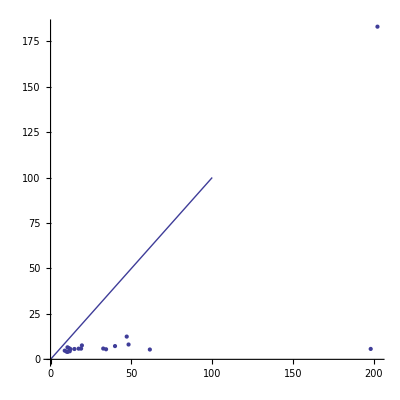

{Knot[15,NonAlternating,111795],6,23,11.77731,17 q+10 q^3+1/(q^5 t^3)+4/(q^3 t^2)+1/(q t^2)+9/(q t)+(4 q)/t+24 q^3 t+16 q^5 t+30 q^5 t^2+24 q^7 t^2+31 q^7 t^3+30 q^9 t^3+30 q^9 t^4+31 q^11 t^4+24 q^11 t^5+30 q^13 t^5+17 q^13 t^6+24 q^15 t^6+10 q^15 t^7+17 q^17 t^7+4 q^17 t^8+10 q^19 t^8+q^19 t^9+4 q^21 t^9+q^23 t^10}

{Knot[15,NonAlternating,111795],6,23,6.212051,17 q+10 q^3+1/(q^5 t^3)+4/(q^3 t^2)+1/(q t^2)+9/(q t)+(4 q)/t+24 q^3 t+16 q^5 t+30 q^5 t^2+24 q^7 t^2+31 q^7 t^3+30 q^9 t^3+30 q^9 t^4+31 q^11 t^4+24 q^11 t^5+30 q^13 t^5+17 q^13 t^6+24 q^15 t^6+10 q^15 t^7+17 q^17 t^7+4 q^17 t^8+10 q^19 t^8+q^19 t^9+4 q^21 t^9+q^23 t^10}

{Knot[15,NonAlternating,111795],6,23,67.666664,KhE q^2+9 q^2 KhC[1]+KhC[1]/(q^2 t^2)+(4 KhC[1])/t+16 q^4 t KhC[1]+24 q^6 t^2 KhC[1]+30 q^8 t^3 KhC[1]+31 q^10 t^4 KhC[1]+30 q^12 t^5 KhC[1]+24 q^14 t^6 KhC[1]+17 q^16 t^7 KhC[1]+10 q^18 t^8 KhC[1]+4 q^20 t^9 KhC[1]+q^22 t^10 KhC[1]}

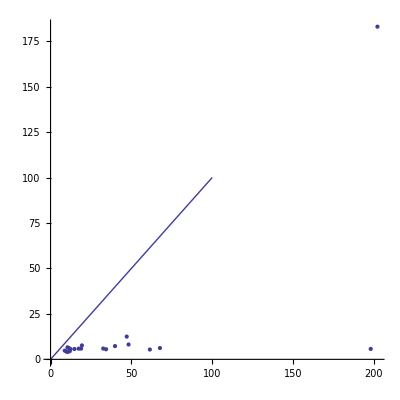

{Knot[15,NonAlternating,162604],6,23,7.052663,14/q^3+17/q+1/(q^19 t^8)+2/(q^17 t^7)+1/(q^15 t^7)+5/(q^15 t^6)+2/(q^13 t^6)+8/(q^13 t^5)+5/(q^11 t^5)+12/(q^11 t^4)+8/(q^9 t^4)+15/(q^9 t^3)+12/(q^7 t^3)+17/(q^7 t^2)+15/(q^5 t^2)+16/(q^5 t)+17/(q^3 t)+(11 t)/q+13 q t+6 q t^2+11 q^3 t^2+4 q^3 t^3+6 q^5 t^3+q^5 t^4+4 q^7 t^4+q^9 t^5}

{Knot[15,NonAlternating,162604],6,23,5.33136,14/q^3+17/q+1/(q^19 t^8)+2/(q^17 t^7)+1/(q^15 t^7)+5/(q^15 t^6)+2/(q^13 t^6)+8/(q^13 t^5)+5/(q^11 t^5)+12/(q^11 t^4)+8/(q^9 t^4)+15/(q^9 t^3)+12/(q^7 t^3)+17/(q^7 t^2)+15/(q^5 t^2)+16/(q^5 t)+17/(q^3 t)+(11 t)/q+13 q t+6 q t^2+11 q^3 t^2+4 q^3 t^3+6 q^5 t^3+q^5 t^4+4 q^7 t^4+q^9 t^5}

{Knot[15,NonAlternating,162604],6,23,10.05577,KhE/q^2+(16 KhC[1])/q^2+KhC[1]/(q^16 t^7)+(2 KhC[1])/(q^14 t^6)+(5 KhC[1])/(q^12 t^5)+(8 KhC[1])/(q^10 t^4)+(12 KhC[1])/(q^8 t^3)+(15 KhC[1])/(q^6 t^2)+(17 KhC[1])/(q^4 t)+13 t KhC[1]+11 q^2 t^2 KhC[1]+6 q^4 t^3 KhC[1]+4 q^6 t^4 KhC[1]+q^8 t^5 KhC[1]}

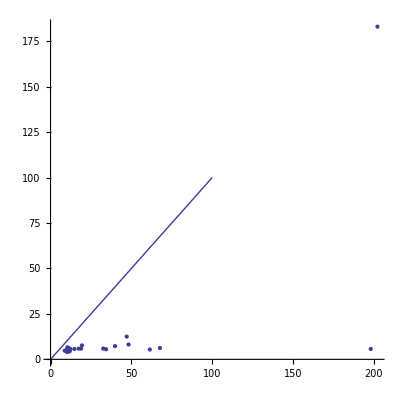

{Knot[15,NonAlternating,20721],6,17,2.57196,7 q+6 q^3+q^5+1/(q^9 t^6)+1/(q^7 t^5)+1/(q^5 t^5)+1/(q^5 t^4)+1/(q^3 t^4)+2/(q^3 t^3)+1/(q t^3)+3/(q^3 t^2)+1/(q t^2)+(2 q)/t^2+4/(q t)+(4 q)/t+q^3/t+8 q^3 t+6 q^5 t+q^7 t+8 q^5 t^2+8 q^7 t^2+7 q^7 t^3+8 q^9 t^3+5 q^9 t^4+7 q^11 t^4+3 q^11 t^5+5 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,20721],6,17,3.24764,7 q+6 q^3+q^5+1/(q^9 t^6)+1/(q^7 t^5)+1/(q^5 t^5)+1/(q^5 t^4)+1/(q^3 t^4)+2/(q^3 t^3)+1/(q t^3)+3/(q^3 t^2)+1/(q t^2)+(2 q)/t^2+4/(q t)+(4 q)/t+q^3/t+8 q^3 t+6 q^5 t+q^7 t+8 q^5 t^2+8 q^7 t^2+7 q^7 t^3+8 q^9 t^3+5 q^9 t^4+7 q^11 t^4+3 q^11 t^5+5 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,20721],6,17,10.14735,KhE q^2+4 q^2 KhC[1]+q^4 KhC[1]+KhC[1]/(q^6 t^5)+KhC[1]/(q^4 t^4)+KhC[1]/(q^2 t^3)+(2 KhC[1])/t^2+(3 KhC[1])/t+(q^2 KhC[1])/t+6 q^4 t KhC[1]+q^6 t KhC[1]+8 q^6 t^2 KhC[1]+8 q^8 t^3 KhC[1]+7 q^10 t^4 KhC[1]+5 q^12 t^5 KhC[1]+3 q^14 t^6 KhC[1]+q^16 t^7 KhC[1]}

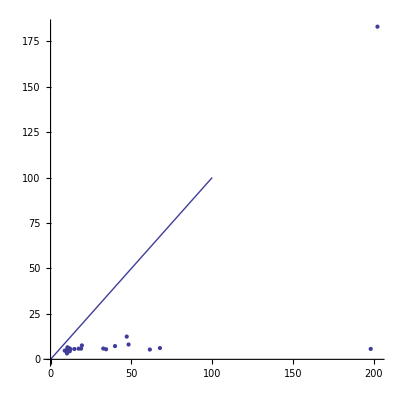

{Knot[15,NonAlternating,76700],6,25,13.36437,3 q^3+3 q^5+2 q^7+1/(q^3 t^4)+1/(q t^3)+q/t^3+(2 q)/t^2+q^3/t^2+(2 q^3)/t+(2 q^5)/t+6 q^5 t+4 q^7 t+2 q^9 t+12 q^7 t^2+7 q^9 t^2+2 q^11 t^2+15 q^9 t^3+13 q^11 t^3+q^13 t^3+19 q^11 t^4+15 q^13 t^4+q^15 t^4+19 q^13 t^5+19 q^15 t^5+17 q^15 t^6+19 q^17 t^6+13 q^17 t^7+17 q^19 t^7+8 q^19 t^8+13 q^21 t^8+4 q^21 t^9+8 q^23 t^9+q^23 t^10+4 q^25 t^10+q^27 t^11}

{Knot[15,NonAlternating,76700],6,25,6.883899,3 q^3+3 q^5+2 q^7+1/(q^3 t^4)+1/(q t^3)+q/t^3+(2 q)/t^2+q^3/t^2+(2 q^3)/t+(2 q^5)/t+6 q^5 t+4 q^7 t+2 q^9 t+12 q^7 t^2+7 q^9 t^2+2 q^11 t^2+15 q^9 t^3+13 q^11 t^3+q^13 t^3+19 q^11 t^4+15 q^13 t^4+q^15 t^4+19 q^13 t^5+19 q^15 t^5+17 q^15 t^6+19 q^17 t^6+13 q^17 t^7+17 q^19 t^7+8 q^19 t^8+13 q^21 t^8+4 q^21 t^9+8 q^23 t^9+q^23 t^10+4 q^25 t^10+q^27 t^11}

{Knot[15,NonAlternating,76700],6,25,53.274416,KhE q^4+2 q^6 KhC[1]+KhC[1]/t^3+(q^2 KhC[1])/t^2+(2 q^4 KhC[1])/t+2 q^6 t KhC[1]+2 q^8 t KhC[1]+6 q^8 t^2 KhC[1]+2 q^10 t^2 KhC[1]+12 q^10 t^3 KhC[1]+q^12 t^3 KhC[1]+15 q^12 t^4 KhC[1]+q^14 t^4 KhC[1]+19 q^14 t^5 KhC[1]+19 q^16 t^6 KhC[1]+17 q^18 t^7 KhC[1]+13 q^20 t^8 KhC[1]+8 q^22 t^9 KhC[1]+4 q^24 t^10 KhC[1]+q^26 t^11 KhC[1]}

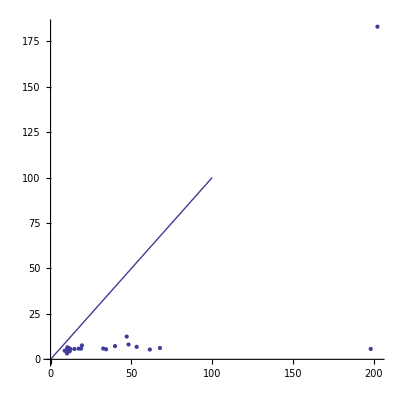

{Knot[15,NonAlternating,21097],6,23,10.71534,6 q^3+3 q^5+(2 q)/t+14 q^5 t+5 q^7 t+23 q^7 t^2+14 q^9 t^2+31 q^9 t^3+23 q^11 t^3+39 q^11 t^4+31 q^13 t^4+38 q^13 t^5+39 q^15 t^5+36 q^15 t^6+38 q^17 t^6+28 q^17 t^7+36 q^19 t^7+19 q^19 t^8+28 q^21 t^8+10 q^21 t^9+19 q^23 t^9+4 q^23 t^10+10 q^25 t^10+q^25 t^11+4 q^27 t^11+q^29 t^12}

{Knot[15,NonAlternating,21097],6,23,4.648471,6 q^3+3 q^5+(2 q)/t+14 q^5 t+5 q^7 t+23 q^7 t^2+14 q^9 t^2+31 q^9 t^3+23 q^11 t^3+39 q^11 t^4+31 q^13 t^4+38 q^13 t^5+39 q^15 t^5+36 q^15 t^6+38 q^17 t^6+28 q^17 t^7+36 q^19 t^7+19 q^19 t^8+28 q^21 t^8+10 q^21 t^9+19 q^23 t^9+4 q^23 t^10+10 q^25 t^10+q^25 t^11+4 q^27 t^11+q^29 t^12}

{Knot[15,NonAlternating,21097],6,23,15.66344,KhE q^4+2 q^4 KhC[1]+5 q^6 t KhC[1]+14 q^8 t^2 KhC[1]+23 q^10 t^3 KhC[1]+31 q^12 t^4 KhC[1]+39 q^14 t^5 KhC[1]+38 q^16 t^6 KhC[1]+36 q^18 t^7 KhC[1]+28 q^20 t^8 KhC[1]+19 q^22 t^9 KhC[1]+10 q^24 t^10 KhC[1]+4 q^26 t^11 KhC[1]+q^28 t^12 KhC[1]}

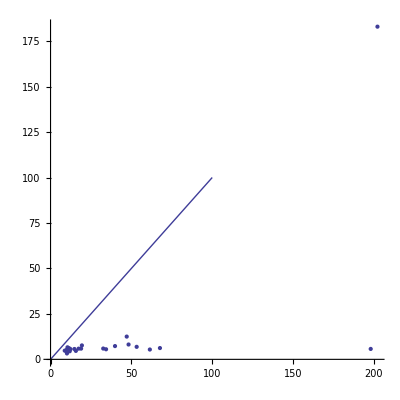

{Knot[15,NonAlternating,148910],8,37,7.184901,18 q+19 q^3+1/(q^13 t^7)+4/(q^11 t^6)+1/(q^9 t^6)+8/(q^9 t^5)+4/(q^7 t^5)+12/(q^7 t^4)+8/(q^5 t^4)+17/(q^5 t^3)+12/(q^3 t^3)+19/(q^3 t^2)+17/(q t^2)+18/(q t)+(19 q)/t+12 q^3 t+17 q^5 t+8 q^5 t^2+12 q^7 t^2+4 q^7 t^3+8 q^9 t^3+q^9 t^4+4 q^11 t^4+q^13 t^5}

{Knot[15,NonAlternating,148910],8,37,7.077813,18 q+19 q^3+1/(q^13 t^7)+4/(q^11 t^6)+1/(q^9 t^6)+8/(q^9 t^5)+4/(q^7 t^5)+12/(q^7 t^4)+8/(q^5 t^4)+17/(q^5 t^3)+12/(q^3 t^3)+19/(q^3 t^2)+17/(q t^2)+18/(q t)+(19 q)/t+12 q^3 t+17 q^5 t+8 q^5 t^2+12 q^7 t^2+4 q^7 t^3+8 q^9 t^3+q^9 t^4+4 q^11 t^4+q^13 t^5}

{Knot[15,NonAlternating,148910],8,37,21.64939,KhE q^2+18 q^2 KhC[1]+KhC[1]/(q^10 t^6)+(4 KhC[1])/(q^8 t^5)+(8 KhC[1])/(q^6 t^4)+(12 KhC[1])/(q^4 t^3)+(17 KhC[1])/(q^2 t^2)+(19 KhC[1])/t+17 q^4 t KhC[1]+12 q^6 t^2 KhC[1]+8 q^8 t^3 KhC[1]+4 q^10 t^4 KhC[1]+q^12 t^5 KhC[1]}

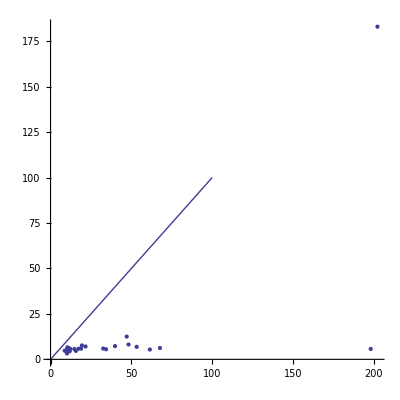

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,39605],6,25,70.028555,$Failed[q,t]}

{Knot[15,Alternating,39605],6,25,34.20137,32 q+24 q^3+1/(q^9 t^5)+3/(q^7 t^4)+1/(q^5 t^4)+8/(q^5 t^3)+3/(q^3 t^3)+15/(q^3 t^2)+8/(q t^2)+23/(q t)+(15 q)/t+37 q^3 t+31 q^5 t+39 q^5 t^2+37 q^7 t^2+36 q^7 t^3+39 q^9 t^3+30 q^9 t^4+36 q^11 t^4+21 q^11 t^5+30 q^13 t^5+14 q^13 t^6+21 q^15 t^6+7 q^15 t^7+14 q^17 t^7+3 q^17 t^8+7 q^19 t^8+q^19 t^9+3 q^21 t^9+q^23 t^10}

{Knot[15,Alternating,39605],6,25,17.14018,KhE q^2+23 q^2 KhC[1]+KhC[1]/(q^6 t^4)+(3 KhC[1])/(q^4 t^3)+(8 KhC[1])/(q^2 t^2)+(15 KhC[1])/t+31 q^4 t KhC[1]+37 q^6 t^2 KhC[1]+39 q^8 t^3 KhC[1]+36 q^10 t^4 KhC[1]+30 q^12 t^5 KhC[1]+21 q^14 t^6 KhC[1]+14 q^16 t^7 KhC[1]+7 q^18 t^8 KhC[1]+3 q^20 t^9 KhC[1]+q^22 t^10 KhC[1]}

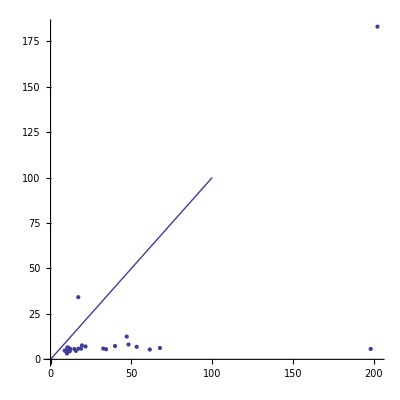

-Graphics-

{Knot[15,NonAlternating,61288],6,21,7.109746,18 q+10 q^3+1/(q^5 t^3)+3/(q^3 t^2)+1/(q t^2)+9/(q t)+(3 q)/t+26 q^3 t+17 q^5 t+32 q^5 t^2+26 q^7 t^2+34 q^7 t^3+32 q^9 t^3+33 q^9 t^4+34 q^11 t^4+26 q^11 t^5+33 q^13 t^5+19 q^13 t^6+26 q^15 t^6+10 q^15 t^7+19 q^17 t^7+4 q^17 t^8+10 q^19 t^8+q^19 t^9+4 q^21 t^9+q^23 t^10}

{Knot[15,NonAlternating,61288],6,21,7.049818,18 q+10 q^3+1/(q^5 t^3)+3/(q^3 t^2)+1/(q t^2)+9/(q t)+(3 q)/t+26 q^3 t+17 q^5 t+32 q^5 t^2+26 q^7 t^2+34 q^7 t^3+32 q^9 t^3+33 q^9 t^4+34 q^11 t^4+26 q^11 t^5+33 q^13 t^5+19 q^13 t^6+26 q^15 t^6+10 q^15 t^7+19 q^17 t^7+4 q^17 t^8+10 q^19 t^8+q^19 t^9+4 q^21 t^9+q^23 t^10}

{Knot[15,NonAlternating,61288],6,21,21.65574,KhE q^2+9 q^2 KhC[1]+KhC[1]/(q^2 t^2)+(3 KhC[1])/t+17 q^4 t KhC[1]+26 q^6 t^2 KhC[1]+32 q^8 t^3 KhC[1]+34 q^10 t^4 KhC[1]+33 q^12 t^5 KhC[1]+26 q^14 t^6 KhC[1]+19 q^16 t^7 KhC[1]+10 q^18 t^8 KhC[1]+4 q^20 t^9 KhC[1]+q^22 t^10 KhC[1]}

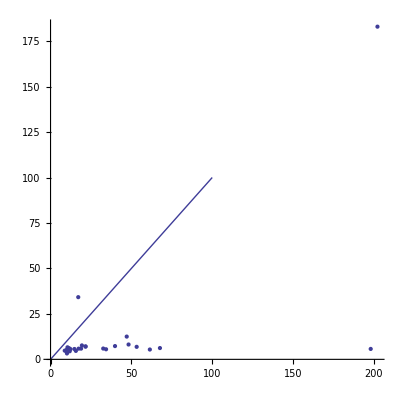

{Knot[15,NonAlternating,163482],4,15,4.342974,2/q^5+9/q^3+9/q+2/(q^17 t^7)+5/(q^15 t^6)+2/(q^13 t^6)+9/(q^13 t^5)+5/(q^11 t^5)+10/(q^11 t^4)+9/(q^9 t^4)+12/(q^9 t^3)+10/(q^7 t^3)+1/(q^9 t^2)+12/(q^7 t^2)+12/(q^5 t^2)+2/(q^7 t)+9/(q^5 t)+12/(q^3 t)+(3 t)/q^3+(5 t)/q+6 q t+(3 t^2)/q+3 q t^2+3 q^3 t^2+2 q t^3+3 q^3 t^3+2 q^3 t^4+2 q^5 t^4+q^5 t^5+2 q^7 t^5+q^9 t^6}

{Knot[15,NonAlternating,163482],4,15,4.965602,2/q^5+9/q^3+9/q+2/(q^17 t^7)+5/(q^15 t^6)+2/(q^13 t^6)+9/(q^13 t^5)+5/(q^11 t^5)+10/(q^11 t^4)+9/(q^9 t^4)+12/(q^9 t^3)+10/(q^7 t^3)+1/(q^9 t^2)+12/(q^7 t^2)+12/(q^5 t^2)+2/(q^7 t)+9/(q^5 t)+12/(q^3 t)+(3 t)/q^3+(5 t)/q+6 q t+(3 t^2)/q+3 q t^2+3 q^3 t^2+2 q t^3+3 q^3 t^3+2 q^3 t^4+2 q^5 t^4+q^5 t^5+2 q^7 t^5+q^9 t^6}

{Knot[15,NonAlternating,163482],4,15,12.7441,KhE/q^2+(2 KhC[1])/q^4+(8 KhC[1])/q^2+(2 KhC[1])/(q^14 t^6)+(5 KhC[1])/(q^12 t^5)+(9 KhC[1])/(q^10 t^4)+(10 KhC[1])/(q^8 t^3)+(12 KhC[1])/(q^6 t^2)+KhC[1]/(q^6 t)+(12 KhC[1])/(q^4 t)+6 t KhC[1]+(2 t KhC[1])/q^2+3 t^2 KhC[1]+3 q^2 t^2 KhC[1]+3 q^2 t^3 KhC[1]+2 q^4 t^4 KhC[1]+2 q^6 t^5 KhC[1]+q^8 t^6 KhC[1]}

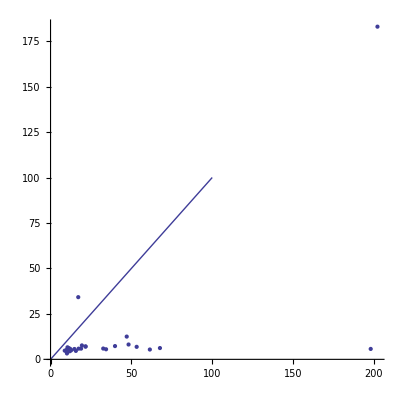

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,46513],8,35,165.51885,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,46513],8,35,51.606729,$Failed[q,t]}

{Knot[15,Alternating,46513],8,35,26.2734,KhE q^4+8 q^4 KhC[1]+KhC[1]/t^2+(4 q^2 KhC[1])/t+16 q^6 t KhC[1]+25 q^8 t^2 KhC[1]+35 q^10 t^3 KhC[1]+42 q^12 t^4 KhC[1]+45 q^14 t^5 KhC[1]+43 q^16 t^6 KhC[1]+37 q^18 t^7 KhC[1]+27 q^20 t^8 KhC[1]+18 q^22 t^9 KhC[1]+10 q^24 t^10 KhC[1]+4 q^26 t^11 KhC[1]+q^28 t^12 KhC[1]}

-Graphics-

{Knot[15,NonAlternating,28667],8,35,30.90364,22 q+14 q^3+1/(q^7 t^4)+3/(q^5 t^3)+1/(q^3 t^3)+9/(q^3 t^2)+3/(q t^2)+13/(q t)+(9 q)/t+25 q^3 t+21 q^5 t+27 q^5 t^2+25 q^7 t^2+26 q^7 t^3+27 q^9 t^3+20 q^9 t^4+26 q^11 t^4+15 q^11 t^5+20 q^13 t^5+8 q^13 t^6+15 q^15 t^6+4 q^15 t^7+8 q^17 t^7+q^17 t^8+4 q^19 t^8+q^21 t^9}

{Knot[15,NonAlternating,28667],8,35,16.46988,22 q+14 q^3+1/(q^7 t^4)+3/(q^5 t^3)+1/(q^3 t^3)+9/(q^3 t^2)+3/(q t^2)+13/(q t)+(9 q)/t+25 q^3 t+21 q^5 t+27 q^5 t^2+25 q^7 t^2+26 q^7 t^3+27 q^9 t^3+20 q^9 t^4+26 q^11 t^4+15 q^11 t^5+20 q^13 t^5+8 q^13 t^6+15 q^15 t^6+4 q^15 t^7+8 q^17 t^7+q^17 t^8+4 q^19 t^8+q^21 t^9}

{Knot[15,NonAlternating,28667],8,35,39.385503,KhE q^2+13 q^2 KhC[1]+KhC[1]/(q^4 t^3)+(3 KhC[1])/(q^2 t^2)+(9 KhC[1])/t+21 q^4 t KhC[1]+25 q^6 t^2 KhC[1]+27 q^8 t^3 KhC[1]+26 q^10 t^4 KhC[1]+20 q^12 t^5 KhC[1]+15 q^14 t^6 KhC[1]+8 q^16 t^7 KhC[1]+4 q^18 t^8 KhC[1]+q^20 t^9 KhC[1]}

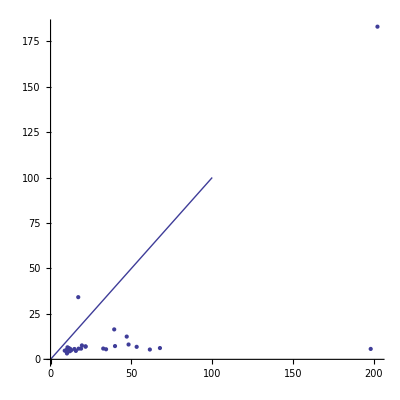

{Knot[15,NonAlternating,67059],6,21,8.46452,20/q^3+26/q+3/(q^17 t^7)+9/(q^15 t^6)+3/(q^13 t^6)+16/(q^13 t^5)+9/(q^11 t^5)+23/(q^11 t^4)+16/(q^9 t^4)+28/(q^9 t^3)+23/(q^7 t^3)+28/(q^7 t^2)+28/(q^5 t^2)+25/(q^5 t)+28/(q^3 t)+(12 t)/q+19 q t+5 q t^2+12 q^3 t^2+q^3 t^3+5 q^5 t^3+q^7 t^4}

{Knot[15,NonAlternating,67059],6,21,5.10976,20/q^3+26/q+3/(q^17 t^7)+9/(q^15 t^6)+3/(q^13 t^6)+16/(q^13 t^5)+9/(q^11 t^5)+23/(q^11 t^4)+16/(q^9 t^4)+28/(q^9 t^3)+23/(q^7 t^3)+28/(q^7 t^2)+28/(q^5 t^2)+25/(q^5 t)+28/(q^3 t)+(12 t)/q+19 q t+5 q t^2+12 q^3 t^2+q^3 t^3+5 q^5 t^3+q^7 t^4}

{Knot[15,NonAlternating,67059],6,21,14.01347,KhE/q^2+(25 KhC[1])/q^2+(3 KhC[1])/(q^14 t^6)+(9 KhC[1])/(q^12 t^5)+(16 KhC[1])/(q^10 t^4)+(23 KhC[1])/(q^8 t^3)+(28 KhC[1])/(q^6 t^2)+(28 KhC[1])/(q^4 t)+19 t KhC[1]+12 q^2 t^2 KhC[1]+5 q^4 t^3 KhC[1]+q^6 t^4 KhC[1]}

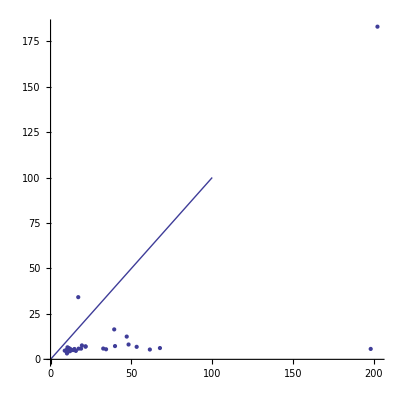

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,14894],8,39,291.54229,$Failed[q,t]}

{Knot[15,NonAlternating,14894],8,39,90.922619,3 q+11 q^3+8 q^5+1/(q^7 t^5)+2/(q^5 t^4)+1/(q^3 t^4)+5/(q^3 t^3)+2/(q t^3)+6/(q t^2)+(5 q)/t^2+1/(q t)+(8 q)/t+(6 q^3)/t+6 q^3 t+9 q^5 t+9 q^7 t+7 q^5 t^2+13 q^7 t^2+7 q^9 t^2+8 q^7 t^3+11 q^9 t^3+7 q^11 t^3+10 q^9 t^4+10 q^11 t^4+4 q^13 t^4+7 q^11 t^5+11 q^13 t^5+2 q^15 t^5+7 q^13 t^6+7 q^15 t^6+q^17 t^6+4 q^15 t^7+7 q^17 t^7+2 q^17 t^8+4 q^19 t^8+q^19 t^9+2 q^21 t^9+q^23 t^10}

{Knot[15,NonAlternating,14894],8,39,59.213099,KhE q^2+q^2 KhC[1]+8 q^4 KhC[1]+KhC[1]/(q^4 t^4)+(2 KhC[1])/(q^2 t^3)+(5 KhC[1])/t^2+(6 q^2 KhC[1])/t+2 q^4 t KhC[1]+9 q^6 t KhC[1]+6 q^6 t^2 KhC[1]+7 q^8 t^2 KhC[1]+7 q^8 t^3 KhC[1]+7 q^10 t^3 KhC[1]+8 q^10 t^4 KhC[1]+4 q^12 t^4 KhC[1]+10 q^12 t^5 KhC[1]+2 q^14 t^5 KhC[1]+7 q^14 t^6 KhC[1]+q^16 t^6 KhC[1]+7 q^16 t^7 KhC[1]+4 q^18 t^8 KhC[1]+2 q^20 t^9 KhC[1]+q^22 t^10 KhC[1]}

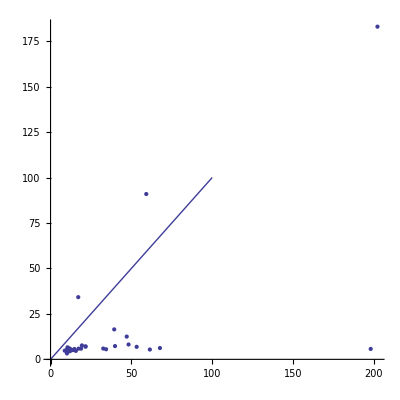

{Knot[15,Alternating,80747],6,23,11.18298,54/q+64 q+1/(q^19 t^9)+4/(q^17 t^8)+1/(q^15 t^8)+11/(q^15 t^7)+4/(q^13 t^7)+22/(q^13 t^6)+11/(q^11 t^6)+38/(q^11 t^5)+22/(q^9 t^5)+52/(q^9 t^4)+38/(q^7 t^4)+63/(q^7 t^3)+52/(q^5 t^3)+68/(q^5 t^2)+63/(q^3 t^2)+63/(q^3 t)+68/(q t)+38 q t+53 q^3 t+23 q^3 t^2+38 q^5 t^2+11 q^5 t^3+23 q^7 t^3+4 q^7 t^4+11 q^9 t^4+q^9 t^5+4 q^11 t^5+q^13 t^6}

{Knot[15,Alternating,80747],6,23,6.390182,54/q+64 q+1/(q^19 t^9)+4/(q^17 t^8)+1/(q^15 t^8)+11/(q^15 t^7)+4/(q^13 t^7)+22/(q^13 t^6)+11/(q^11 t^6)+38/(q^11 t^5)+22/(q^9 t^5)+52/(q^9 t^4)+38/(q^7 t^4)+63/(q^7 t^3)+52/(q^5 t^3)+68/(q^5 t^2)+63/(q^3 t^2)+63/(q^3 t)+68/(q t)+38 q t+53 q^3 t+23 q^3 t^2+38 q^5 t^2+11 q^5 t^3+23 q^7 t^3+4 q^7 t^4+11 q^9 t^4+q^9 t^5+4 q^11 t^5+q^13 t^6}

{Knot[15,Alternating,80747],6,23,59.066944,KhE+63 KhC[1]+KhC[1]/(q^16 t^8)+(4 KhC[1])/(q^14 t^7)+(11 KhC[1])/(q^12 t^6)+(22 KhC[1])/(q^10 t^5)+(38 KhC[1])/(q^8 t^4)+(52 KhC[1])/(q^6 t^3)+(63 KhC[1])/(q^4 t^2)+(68 KhC[1])/(q^2 t)+53 q^2 t KhC[1]+38 q^4 t^2 KhC[1]+23 q^6 t^3 KhC[1]+11 q^8 t^4 KhC[1]+4 q^10 t^5 KhC[1]+q^12 t^6 KhC[1]}

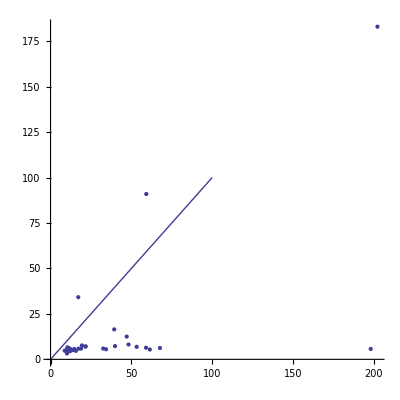

{Knot[15,NonAlternating,65272],6,23,14.97938,23/q^3+24/q+1/(q^15 t^6)+4/(q^13 t^5)+1/(q^11 t^5)+9/(q^11 t^4)+4/(q^9 t^4)+15/(q^9 t^3)+9/(q^7 t^3)+20/(q^7 t^2)+15/(q^5 t^2)+23/(q^5 t)+20/(q^3 t)+(20 t)/q+22 q t+15 q t^2+20 q^3 t^2+9 q^3 t^3+15 q^5 t^3+4 q^5 t^4+9 q^7 t^4+q^7 t^5+4 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,65272],6,23,7.165891,23/q^3+24/q+1/(q^15 t^6)+4/(q^13 t^5)+1/(q^11 t^5)+9/(q^11 t^4)+4/(q^9 t^4)+15/(q^9 t^3)+9/(q^7 t^3)+20/(q^7 t^2)+15/(q^5 t^2)+23/(q^5 t)+20/(q^3 t)+(20 t)/q+22 q t+15 q t^2+20 q^3 t^2+9 q^3 t^3+15 q^5 t^3+4 q^5 t^4+9 q^7 t^4+q^7 t^5+4 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,65272],6,23,12.45562,KhE/q^2+(23 KhC[1])/q^2+KhC[1]/(q^12 t^5)+(4 KhC[1])/(q^10 t^4)+(9 KhC[1])/(q^8 t^3)+(15 KhC[1])/(q^6 t^2)+(20 KhC[1])/(q^4 t)+22 t KhC[1]+20 q^2 t^2 KhC[1]+15 q^4 t^3 KhC[1]+9 q^6 t^4 KhC[1]+4 q^8 t^5 KhC[1]+q^10 t^6 KhC[1]}

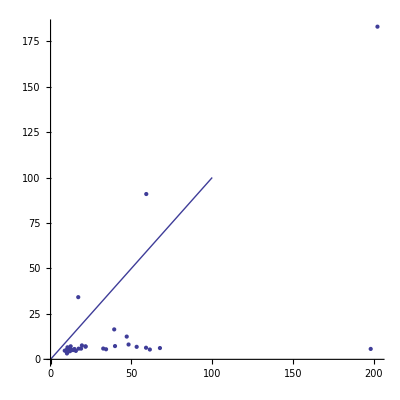

{Knot[15,NonAlternating,147992],6,25,7.590873,39 q+38 q^3+1/(q^11 t^6)+5/(q^9 t^5)+1/(q^7 t^5)+12/(q^7 t^4)+5/(q^5 t^4)+22/(q^5 t^3)+12/(q^3 t^3)+30/(q^3 t^2)+22/(q t^2)+37/(q t)+(30 q)/t+36 q^3 t+38 q^5 t+29 q^5 t^2+36 q^7 t^2+18 q^7 t^3+29 q^9 t^3+11 q^9 t^4+18 q^11 t^4+3 q^11 t^5+11 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,147992],6,25,6.737771,39 q+38 q^3+1/(q^11 t^6)+5/(q^9 t^5)+1/(q^7 t^5)+12/(q^7 t^4)+5/(q^5 t^4)+22/(q^5 t^3)+12/(q^3 t^3)+30/(q^3 t^2)+22/(q t^2)+37/(q t)+(30 q)/t+36 q^3 t+38 q^5 t+29 q^5 t^2+36 q^7 t^2+18 q^7 t^3+29 q^9 t^3+11 q^9 t^4+18 q^11 t^4+3 q^11 t^5+11 q^13 t^5+q^13 t^6+3 q^15 t^6+q^17 t^7}

{Knot[15,NonAlternating,147992],6,25,48.15228,KhE q^2+37 q^2 KhC[1]+KhC[1]/(q^8 t^5)+(5 KhC[1])/(q^6 t^4)+(12 KhC[1])/(q^4 t^3)+(22 KhC[1])/(q^2 t^2)+(30 KhC[1])/t+38 q^4 t KhC[1]+36 q^6 t^2 KhC[1]+29 q^8 t^3 KhC[1]+18 q^10 t^4 KhC[1]+11 q^12 t^5 KhC[1]+3 q^14 t^6 KhC[1]+q^16 t^7 KhC[1]}

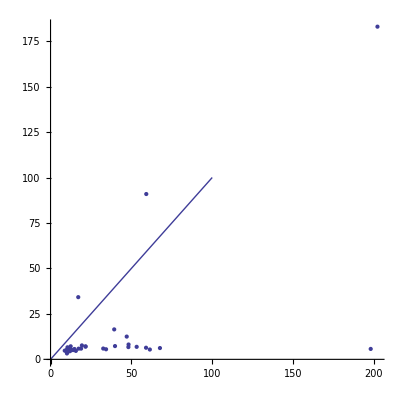

{Knot[15,NonAlternating,70427],8,35,16.70138,25/q+26 q+1/(q^15 t^7)+3/(q^13 t^6)+1/(q^11 t^6)+7/(q^11 t^5)+3/(q^9 t^5)+13/(q^9 t^4)+7/(q^7 t^4)+18/(q^7 t^3)+13/(q^5 t^3)+24/(q^5 t^2)+18/(q^3 t^2)+25/(q^3 t)+24/(q t)+21 q t+24 q^3 t+14 q^3 t^2+21 q^5 t^2+9 q^5 t^3+14 q^7 t^3+4 q^7 t^4+9 q^9 t^4+q^9 t^5+4 q^11 t^5+q^13 t^6}

{Knot[15,NonAlternating,70427],8,35,6.577672,25/q+26 q+1/(q^15 t^7)+3/(q^13 t^6)+1/(q^11 t^6)+7/(q^11 t^5)+3/(q^9 t^5)+13/(q^9 t^4)+7/(q^7 t^4)+18/(q^7 t^3)+13/(q^5 t^3)+24/(q^5 t^2)+18/(q^3 t^2)+25/(q^3 t)+24/(q t)+21 q t+24 q^3 t+14 q^3 t^2+21 q^5 t^2+9 q^5 t^3+14 q^7 t^3+4 q^7 t^4+9 q^9 t^4+q^9 t^5+4 q^11 t^5+q^13 t^6}

{Knot[15,NonAlternating,70427],8,35,536.427138,KhE+25 KhC[1]+KhC[1]/(q^12 t^6)+(3 KhC[1])/(q^10 t^5)+(7 KhC[1])/(q^8 t^4)+(13 KhC[1])/(q^6 t^3)+(18 KhC[1])/(q^4 t^2)+(24 KhC[1])/(q^2 t)+24 q^2 t KhC[1]+21 q^4 t^2 KhC[1]+14 q^6 t^3 KhC[1]+9 q^8 t^4 KhC[1]+4 q^10 t^5 KhC[1]+q^12 t^6 KhC[1]}

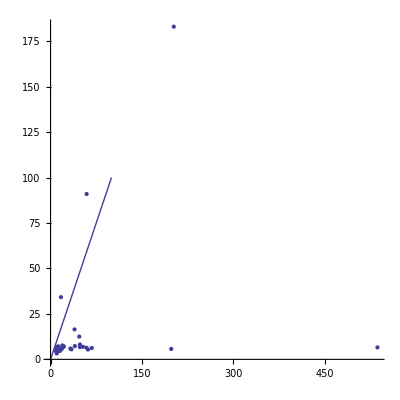

{Knot[15,NonAlternating,54875],6,23,9.979942,29/q+27 q+1/(q^13 t^6)+3/(q^11 t^5)+1/(q^9 t^5)+8/(q^9 t^4)+3/(q^7 t^4)+14/(q^7 t^3)+8/(q^5 t^3)+21/(q^5 t^2)+14/(q^3 t^2)+26/(q^3 t)+21/(q t)+27 q t+28 q^3 t+22 q^3 t^2+27 q^5 t^2+16 q^5 t^3+22 q^7 t^3+9 q^7 t^4+16 q^9 t^4+4 q^9 t^5+9 q^11 t^5+q^11 t^6+4 q^13 t^6+q^15 t^7}

{Knot[15,NonAlternating,54875],6,23,5.003532,29/q+27 q+1/(q^13 t^6)+3/(q^11 t^5)+1/(q^9 t^5)+8/(q^9 t^4)+3/(q^7 t^4)+14/(q^7 t^3)+8/(q^5 t^3)+21/(q^5 t^2)+14/(q^3 t^2)+26/(q^3 t)+21/(q t)+27 q t+28 q^3 t+22 q^3 t^2+27 q^5 t^2+16 q^5 t^3+22 q^7 t^3+9 q^7 t^4+16 q^9 t^4+4 q^9 t^5+9 q^11 t^5+q^11 t^6+4 q^13 t^6+q^15 t^7}

{Knot[15,NonAlternating,54875],6,23,19.94538,KhE+26 KhC[1]+KhC[1]/(q^10 t^5)+(3 KhC[1])/(q^8 t^4)+(8 KhC[1])/(q^6 t^3)+(14 KhC[1])/(q^4 t^2)+(21 KhC[1])/(q^2 t)+28 q^2 t KhC[1]+27 q^4 t^2 KhC[1]+22 q^6 t^3 KhC[1]+16 q^8 t^4 KhC[1]+9 q^10 t^5 KhC[1]+4 q^12 t^6 KhC[1]+q^14 t^7 KhC[1]}

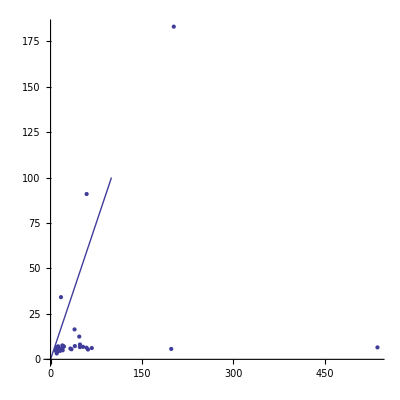

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,35849],8,33,1512.59597,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,35849],8,33,67.608817,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

{Knot[15,Alternating,35849],8,33,219.2125,KnotTheory`UniversalKh`Private`DecomposeComplex[KnotTheory`UniversalKh`Private`GradingsList[$Failed],KnotTheory`UniversalKh`Private`Matrices[$Failed]]}

-Graphics-

{Knot[15,NonAlternating,106054],6,23,7.874669,8/q^5+15/q^3+1/(q^25 t^10)+3/(q^23 t^9)+1/(q^21 t^9)+8/(q^21 t^8)+3/(q^19 t^8)+15/(q^19 t^7)+8/(q^17 t^7)+21/(q^17 t^6)+15/(q^15 t^6)+26/(q^15 t^5)+21/(q^13 t^5)+27/(q^13 t^4)+26/(q^11 t^4)+26/(q^11 t^3)+27/(q^9 t^3)+20/(q^9 t^2)+26/(q^7 t^2)+14/(q^7 t)+20/(q^5 t)+(3 t)/q^3+(7 t)/q+t^2/q+3 q t^2+q^3 t^3}

{Knot[15,NonAlternating,106054],6,23,7.384231,8/q^5+15/q^3+1/(q^25 t^10)+3/(q^23 t^9)+1/(q^21 t^9)+8/(q^21 t^8)+3/(q^19 t^8)+15/(q^19 t^7)+8/(q^17 t^7)+21/(q^17 t^6)+15/(q^15 t^6)+26/(q^15 t^5)+21/(q^13 t^5)+27/(q^13 t^4)+26/(q^11 t^4)+26/(q^11 t^3)+27/(q^9 t^3)+20/(q^9 t^2)+26/(q^7 t^2)+14/(q^7 t)+20/(q^5 t)+(3 t)/q^3+(7 t)/q+t^2/q+3 q t^2+q^3 t^3}

{Knot[15,NonAlternating,106054],6,23,20.03102,KhE/q^4+(14 KhC[1])/q^4+KhC[1]/(q^22 t^9)+(3 KhC[1])/(q^20 t^8)+(8 KhC[1])/(q^18 t^7)+(15 KhC[1])/(q^16 t^6)+(21 KhC[1])/(q^14 t^5)+(26 KhC[1])/(q^12 t^4)+(27 KhC[1])/(q^10 t^3)+(26 KhC[1])/(q^8 t^2)+(20 KhC[1])/(q^6 t)+(7 t KhC[1])/q^2+3 t^2 KhC[1]+q^2 t^3 KhC[1]}

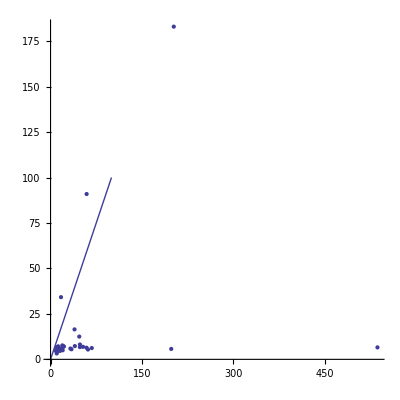

{Knot[15,NonAlternating,48773],8,37,9.235397,8/q+10 q+1/(q^17 t^8)+1/(q^15 t^7)+1/(q^13 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+5/(q^11 t^5)+4/(q^9 t^5)+8/(q^9 t^4)+5/(q^7 t^4)+9/(q^7 t^3)+8/(q^5 t^3)+10/(q^5 t^2)+9/(q^3 t^2)+9/(q^3 t)+10/(q t)+6 q t+7 q^3 t+2 q^3 t^2+6 q^5 t^2+2 q^5 t^3+2 q^7 t^3+2 q^9 t^4}

{Knot[15,NonAlternating,48773],8,37,8.695275,8/q+10 q+1/(q^17 t^8)+1/(q^15 t^7)+1/(q^13 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+5/(q^11 t^5)+4/(q^9 t^5)+8/(q^9 t^4)+5/(q^7 t^4)+9/(q^7 t^3)+8/(q^5 t^3)+10/(q^5 t^2)+9/(q^3 t^2)+9/(q^3 t)+10/(q t)+6 q t+7 q^3 t+2 q^3 t^2+6 q^5 t^2+2 q^5 t^3+2 q^7 t^3+2 q^9 t^4}

{Knot[15,NonAlternating,48773],8,37,32.29291,KhE+9 KhC[1]+KhC[1]/(q^14 t^7)+KhC[1]/(q^12 t^6)+(4 KhC[1])/(q^10 t^5)+(5 KhC[1])/(q^8 t^4)+(8 KhC[1])/(q^6 t^3)+(9 KhC[1])/(q^4 t^2)+(10 KhC[1])/(q^2 t)+7 q^2 t KhC[1]+6 q^4 t^2 KhC[1]+2 q^6 t^3 KhC[1]+2 q^8 t^4 KhC[1]}

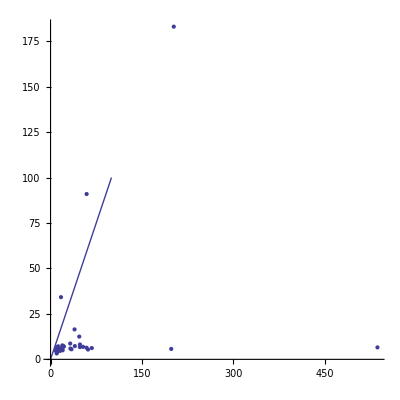

{Knot[15,NonAlternating,135498],8,35,11.21575,15/q^3+14/q+2/(q^13 t^5)+4/(q^11 t^4)+2/(q^9 t^4)+8/(q^9 t^3)+4/(q^7 t^3)+12/(q^7 t^2)+8/(q^5 t^2)+13/(q^5 t)+12/(q^3 t)+(13 t)/q+14 q t+10 q t^2+13 q^3 t^2+7 q^3 t^3+10 q^5 t^3+3 q^5 t^4+7 q^7 t^4+q^7 t^5+3 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,135498],8,35,9.310119,15/q^3+14/q+2/(q^13 t^5)+4/(q^11 t^4)+2/(q^9 t^4)+8/(q^9 t^3)+4/(q^7 t^3)+12/(q^7 t^2)+8/(q^5 t^2)+13/(q^5 t)+12/(q^3 t)+(13 t)/q+14 q t+10 q t^2+13 q^3 t^2+7 q^3 t^3+10 q^5 t^3+3 q^5 t^4+7 q^7 t^4+q^7 t^5+3 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,135498],8,35,11.70158,KhE/q^2+(13 KhC[1])/q^2+(2 KhC[1])/(q^10 t^4)+(4 KhC[1])/(q^8 t^3)+(8 KhC[1])/(q^6 t^2)+(12 KhC[1])/(q^4 t)+14 t KhC[1]+13 q^2 t^2 KhC[1]+10 q^4 t^3 KhC[1]+7 q^6 t^4 KhC[1]+3 q^8 t^5 KhC[1]+q^10 t^6 KhC[1]}

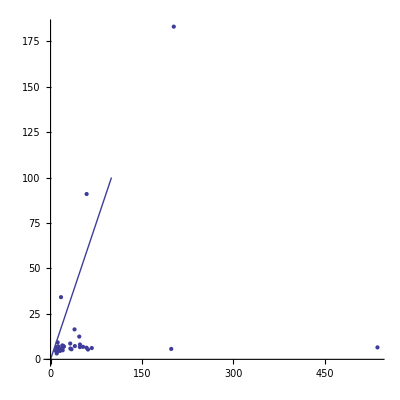

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,29631],8,37,191.23829,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,29631],8,37,56.927752,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

{Knot[15,Alternating,29631],8,37,160.91381,KnotTheory`UniversalKh`Private`DecomposeComplex[KnotTheory`UniversalKh`Private`GradingsList[$Failed],KnotTheory`UniversalKh`Private`Matrices[$Failed]]}

-Graphics-

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,25015],8,35,66.424601,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,25015],8,35,56.973875,$Failed[q,t]}

{Knot[15,NonAlternating,25015],8,35,255.89388,KhE q^4+17 q^4 KhC[1]+KhC[1]/(q^2 t^3)+(3 KhC[1])/t^2+(9 q^2 KhC[1])/t+28 q^6 t KhC[1]+37 q^8 t^2 KhC[1]+43 q^10 t^3 KhC[1]+42 q^12 t^4 KhC[1]+37 q^14 t^5 KhC[1]+28 q^16 t^6 KhC[1]+17 q^18 t^7 KhC[1]+8 q^20 t^8 KhC[1]+2 q^22 t^9 KhC[1]}

-Graphics-

{Knot[15,Alternating,40339],6,23,10.38033,56/q+47 q+1/(q^13 t^6)+4/(q^11 t^5)+1/(q^9 t^5)+10/(q^9 t^4)+4/(q^7 t^4)+21/(q^7 t^3)+10/(q^5 t^3)+33/(q^5 t^2)+21/(q^3 t^2)+46/(q^3 t)+33/(q t)+59 q t+55 q^3 t+56 q^3 t^2+59 q^5 t^2+46 q^5 t^3+56 q^7 t^3+34 q^7 t^4+46 q^9 t^4+21 q^9 t^5+34 q^11 t^5+11 q^11 t^6+21 q^13 t^6+4 q^13 t^7+11 q^15 t^7+q^15 t^8+4 q^17 t^8+q^19 t^9}

{Knot[15,Alternating,40339],6,23,8.585257,56/q+47 q+1/(q^13 t^6)+4/(q^11 t^5)+1/(q^9 t^5)+10/(q^9 t^4)+4/(q^7 t^4)+21/(q^7 t^3)+10/(q^5 t^3)+33/(q^5 t^2)+21/(q^3 t^2)+46/(q^3 t)+33/(q t)+59 q t+55 q^3 t+56 q^3 t^2+59 q^5 t^2+46 q^5 t^3+56 q^7 t^3+34 q^7 t^4+46 q^9 t^4+21 q^9 t^5+34 q^11 t^5+11 q^11 t^6+21 q^13 t^6+4 q^13 t^7+11 q^15 t^7+q^15 t^8+4 q^17 t^8+q^19 t^9}

{Knot[15,Alternating,40339],6,23,109.07753,KhE+46 KhC[1]+KhC[1]/(q^10 t^5)+(4 KhC[1])/(q^8 t^4)+(10 KhC[1])/(q^6 t^3)+(21 KhC[1])/(q^4 t^2)+(33 KhC[1])/(q^2 t)+55 q^2 t KhC[1]+59 q^4 t^2 KhC[1]+56 q^6 t^3 KhC[1]+46 q^8 t^4 KhC[1]+34 q^10 t^5 KhC[1]+21 q^12 t^6 KhC[1]+11 q^14 t^7 KhC[1]+4 q^16 t^8 KhC[1]+q^18 t^9 KhC[1]}

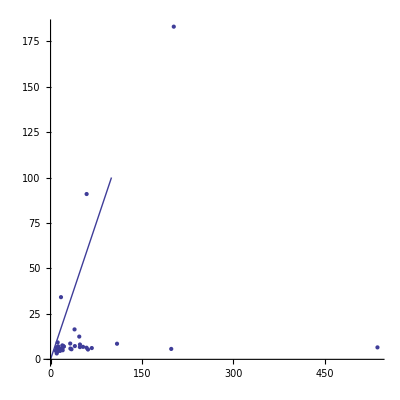

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,4860],8,37,105.22818,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,Alternating,4860],8,37,250.33311,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

{Knot[15,Alternating,4860],8,37,147.93876,KnotTheory`UniversalKh`Private`DecomposeComplex[KnotTheory`UniversalKh`Private`GradingsList[$Failed],KnotTheory`UniversalKh`Private`Matrices[$Failed]]}

-Graphics-

{Knot[15,NonAlternating,2371],6,23,10.63831,7/q^3+10/q+8 q+1/(q^19 t^9)+3/(q^17 t^8)+1/(q^15 t^8)+7/(q^15 t^7)+3/(q^13 t^7)+10/(q^13 t^6)+7/(q^11 t^6)+13/(q^11 t^5)+10/(q^9 t^5)+14/(q^9 t^4)+13/(q^7 t^4)+2/(q^9 t^3)+13/(q^7 t^3)+14/(q^5 t^3)+4/(q^7 t^2)+13/(q^5 t^2)+13/(q^3 t^2)+5/(q^5 t)+11/(q^3 t)+11/(q t)+(7 t)/q+8 q t+4 q^3 t+6 q t^2+7 q^3 t^2+q^5 t^2+5 q^3 t^3+6 q^5 t^3+3 q^5 t^4+5 q^7 t^4+q^7 t^5+3 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,2371],6,23,9.157364,7/q^3+10/q+8 q+1/(q^19 t^9)+3/(q^17 t^8)+1/(q^15 t^8)+7/(q^15 t^7)+3/(q^13 t^7)+10/(q^13 t^6)+7/(q^11 t^6)+13/(q^11 t^5)+10/(q^9 t^5)+14/(q^9 t^4)+13/(q^7 t^4)+2/(q^9 t^3)+13/(q^7 t^3)+14/(q^5 t^3)+4/(q^7 t^2)+13/(q^5 t^2)+13/(q^3 t^2)+5/(q^5 t)+11/(q^3 t)+11/(q t)+(7 t)/q+8 q t+4 q^3 t+6 q t^2+7 q^3 t^2+q^5 t^2+5 q^3 t^3+6 q^5 t^3+3 q^5 t^4+5 q^7 t^4+q^7 t^5+3 q^9 t^5+q^11 t^6}

{Knot[15,NonAlternating,2371],6,23,36.119206,KhE+7 KhC[1]+(5 KhC[1])/q^2+KhC[1]/(q^16 t^8)+(3 KhC[1])/(q^14 t^7)+(7 KhC[1])/(q^12 t^6)+(10 KhC[1])/(q^10 t^5)+(13 KhC[1])/(q^8 t^4)+(14 KhC[1])/(q^6 t^3)+(2 KhC[1])/(q^6 t^2)+(13 KhC[1])/(q^4 t^2)+(4 KhC[1])/(q^4 t)+(11 KhC[1])/(q^2 t)+7 t KhC[1]+4 q^2 t KhC[1]+7 q^2 t^2 KhC[1]+q^4 t^2 KhC[1]+6 q^4 t^3 KhC[1]+5 q^6 t^4 KhC[1]+3 q^8 t^5 KhC[1]+q^10 t^6 KhC[1]}

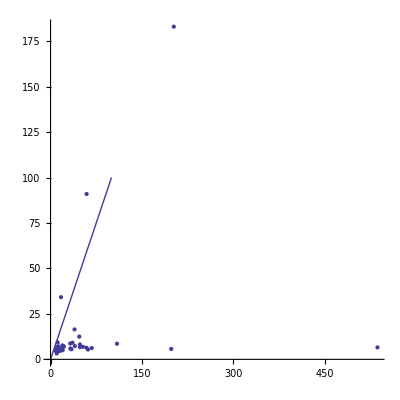

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,71360],10,49,124.84786,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,71360],10,49,139.87363,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/bin:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-cli-1.0.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-io-1.2.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/commons-logging-1.1.jar:/Users/scott/projects/KnotTheory/trunk/KnotTheory/JavaKh-v2/jars/log4j-1.2.12.jar"  org.katlas.JavaKh.JavaKh -U -Q < pd

{Knot[15,NonAlternating,71360],10,49,341.50749,KnotTheory`UniversalKh`Private`DecomposeComplex[KnotTheory`UniversalKh`Private`GradingsList[$Failed],KnotTheory`UniversalKh`Private`Matrices[$Failed]]}

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
({benchmark["JavaKh-v1",Khv1,#],benchmark["JavaKh-v2",Khv2,#],benchmark["UniversalKh",KhU,#]};Print[benchmarkComparision2])&/@RandomSample[AllKnots[{15,15}],40]
```

{Knot[15,Alternating,23519],4,15,9.375,65/q+61 q+1/(q^15 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+10/(q^11 t^5)+4/(q^9 t^5)+21/(q^9 t^4)+10/(q^7 t^4)+35/(q^7 t^3)+21/(q^5 t^3)+49/(q^5 t^2)+35/(q^3 t^2)+60/(q^3 t)+49/(q t)+62 q t+64 q^3 t+52 q^3 t^2+62 q^5 t^2+38 q^5 t^3+52 q^7 t^3+24 q^7 t^4+38 q^9 t^4+12 q^9 t^5+24 q^11 t^5+5 q^11 t^6+12 q^13 t^6+q^13 t^7+5 q^15 t^7+q^17 t^8}

{Knot[15,Alternating,23519],4,15,3.203125,65/q+61 q+1/(q^15 t^7)+4/(q^13 t^6)+1/(q^11 t^6)+10/(q^11 t^5)+4/(q^9 t^5)+21/(q^9 t^4)+10/(q^7 t^4)+35/(q^7 t^3)+21/(q^5 t^3)+49/(q^5 t^2)+35/(q^3 t^2)+60/(q^3 t)+49/(q t)+62 q t+64 q^3 t+52 q^3 t^2+62 q^5 t^2+38 q^5 t^3+52 q^7 t^3+24 q^7 t^4+38 q^9 t^4+12 q^9 t^5+24 q^11 t^5+5 q^11 t^6+12 q^13 t^6+q^13 t^7+5 q^15 t^7+q^17 t^8}

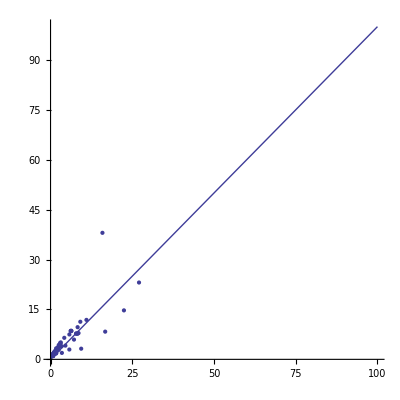

{Knot[15,NonAlternating,134534],6,25,0.921875,4 q^3+2 q^5+q^7+1/(q^3 t^4)+q/t^3+q/t^2+q/t+q^3/t+q^5/t+4 q^5 t+4 q^7 t+6 q^7 t^2+4 q^9 t^2+q^11 t^2+6 q^9 t^3+6 q^11 t^3+6 q^11 t^4+6 q^13 t^4+4 q^13 t^5+6 q^15 t^5+3 q^15 t^6+4 q^17 t^6+q^17 t^7+3 q^19 t^7+q^21 t^8}

{Knot[15,NonAlternating,134534],6,25,1.875,4 q^3+2 q^5+q^7+1/(q^3 t^4)+q/t^3+q/t^2+q/t+q^3/t+q^5/t+4 q^5 t+4 q^7 t+6 q^7 t^2+4 q^9 t^2+q^11 t^2+6 q^9 t^3+6 q^11 t^3+6 q^11 t^4+6 q^13 t^4+4 q^13 t^5+6 q^15 t^5+3 q^15 t^6+4 q^17 t^6+q^17 t^7+3 q^19 t^7+q^21 t^8}

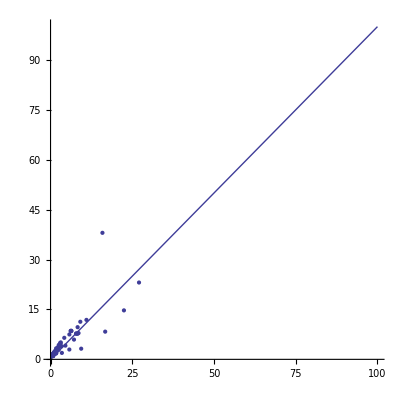

{Knot[15,Alternating,28027],4,15,12.5,69 q+56 q^3+1/(q^11 t^6)+4/(q^9 t^5)+1/(q^7 t^5)+11/(q^7 t^4)+4/(q^5 t^4)+24/(q^5 t^3)+11/(q^3 t^3)+39/(q^3 t^2)+24/(q t^2)+55/(q t)+(39 q)/t+73 q^3 t+68 q^5 t+70 q^5 t^2+73 q^7 t^2+58 q^7 t^3+70 q^9 t^3+43 q^9 t^4+58 q^11 t^4+26 q^11 t^5+43 q^13 t^5+13 q^13 t^6+26 q^15 t^6+5 q^15 t^7+13 q^17 t^7+q^17 t^8+5 q^19 t^8+q^21 t^9}

{Knot[15,Alternating,28027],4,15,3.65625,69 q+56 q^3+1/(q^11 t^6)+4/(q^9 t^5)+1/(q^7 t^5)+11/(q^7 t^4)+4/(q^5 t^4)+24/(q^5 t^3)+11/(q^3 t^3)+39/(q^3 t^2)+24/(q t^2)+55/(q t)+(39 q)/t+73 q^3 t+68 q^5 t+70 q^5 t^2+73 q^7 t^2+58 q^7 t^3+70 q^9 t^3+43 q^9 t^4+58 q^11 t^4+26 q^11 t^5+43 q^13 t^5+13 q^13 t^6+26 q^15 t^6+5 q^15 t^7+13 q^17 t^7+q^17 t^8+5 q^19 t^8+q^21 t^9}

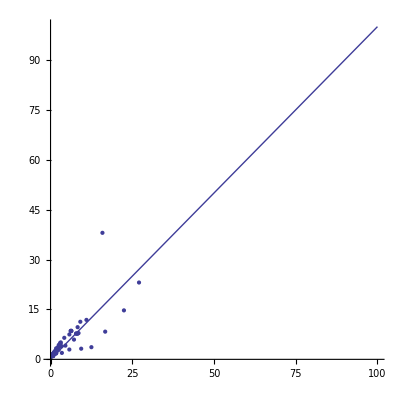

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh1"  org.katlas.JavaKh.JavaKh -mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.LCCC.<init>(LCCC.java:19)
	at org.katlas.JavaKh.LCCC.compose(LCCC.java:152)
	at org.katlas.JavaKh.Komplex.compose(Komplex.java:1176)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1092)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:43)
Exception in thread "main" java.lang.OutOfMemoryError: Java heap space
	at org.katlas.JavaKh.CannedCobordismImpl.reverseMaps(CannedCobordismImpl.java:163)
	at org.katlas.JavaKh.CannedCobordismImpl.composeWithoutCache(CannedCobordismImpl.java:555)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:341)
	at org.katlas.JavaKh.CannedCobordismImpl.compose(CannedCobordismImpl.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:142)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:163)
	at org.katlas.JavaKh.LCCCMap.compose(LCCCMap.java:1)
	at org.katlas.JavaKh.algebra.implementations.LinearComboMap.compose(LinearComboMap.java:1)
	at org.katlas.JavaKh.CobMatrix.compose(CobMatrix.java:173)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1285)
	at org.katlas.JavaKh.Komplex.blockReductionLemma(Komplex.java:1014)
	at org.katlas.JavaKh.Komplex.reduce(Komplex.java:506)
	at org.katlas.JavaKh.Komplex.generateFast(Komplex.java:1659)
	at org.katlas.JavaKh.JavaKh.main(JavaKh.java:111)

{Knot[15,NonAlternating,128085],8,35,818.328125,$Failed[q,t]}

Something went wrong running JavaKh; nothing was returned. The command line was:

!java -classpath "C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\bin;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-cli-1.0.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-io-1.2.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\commons-logging-1.1.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\log4j-1.2.12.jar;C:\scott\projects\KnotTheory\trunk\KnotTheory\JavaKh2\jars\trove-2.0.4.jar"  org.katlas.JavaKh.JavaKh --mod 0 < pd 2> JavaKh.log

There may have been an error log produced by Java:

{Knot[15,NonAlternating,128085],8,35,140.359375,$Failed[q,t]}

-Graphics-

```mathematica
({benchmark["JavaKh-v1",Khv1,#],benchmark["JavaKh-v2",Khv2,#]};Print[benchmarkComparision])&/@RandomSample[AllKnots[{12,15}],100]
```

```mathematica
Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[BenchmarkData["FastKh"],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

{{{10,1.359375},{10,1.65625},{10,1.171875}},{{11,1.515625},{11,1.25}},{{12,1.171875},{12,2.078125},{12,1.359375}},{{13,1.34375},{13,1.234375}}}

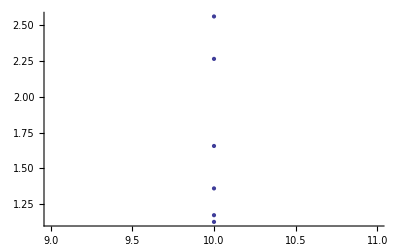
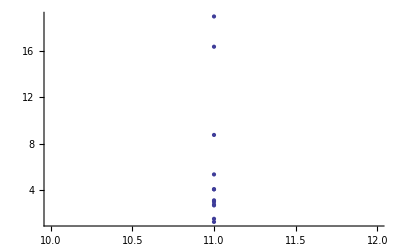
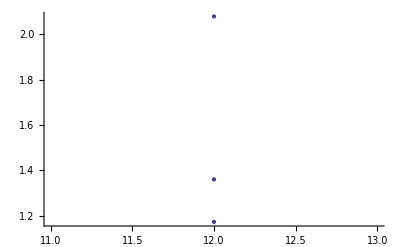
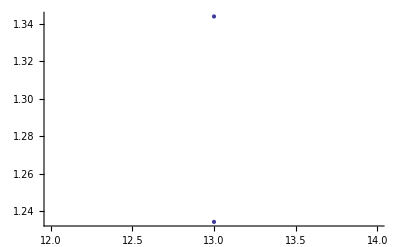

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[BenchmarkData["FastKh"],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

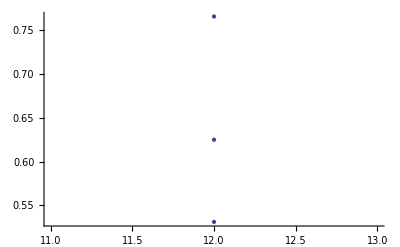
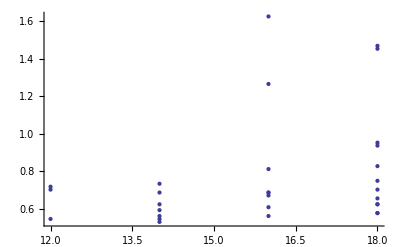
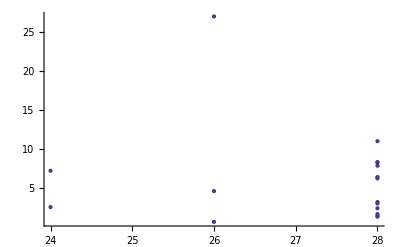
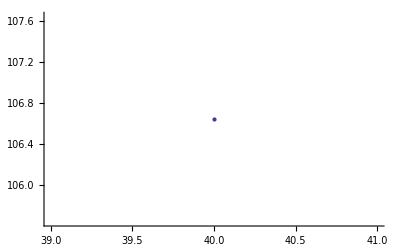

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[DeleteCases[BenchmarkData["JavaKh-v1"],$Failed[q,t]],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

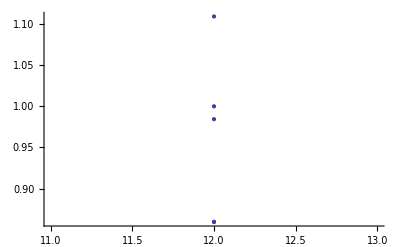
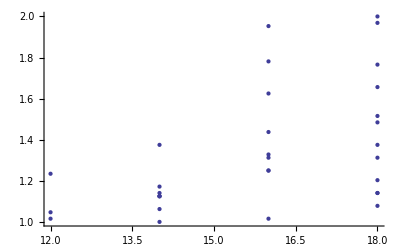
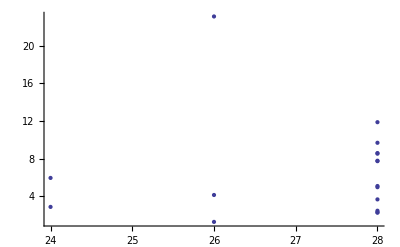
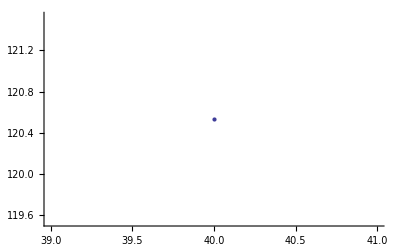

```mathematica
ListPlot/@Map[{#⟦3⟧,#⟦4⟧}&,Split[SortBy[DeleteCases[BenchmarkData["JavaKh-v2"],$Failed[q,t]],#⟦2⟧&],#1⟦2⟧==#2⟦2⟧&],{2}]
```

```mathematica
RandomKnot[n_]:=Module[{k},
k=Random[Integer,{1,NumberOfKnots[n]}];
If[k≤NumberOfKnots[n,Alternating],
Knot[n,Alternating,k],
Knot[n,NonAlternating,k-NumberOfKnots[n,Alternating]]
]
]
```

```mathematica
QuantumKnotInvariantSplit[K,Γ,Irrep[Γ][λ]]
```

```mathematica
QuantumKnotInvariantSplit[#,Subscript[A, 2],Irrep[Subscript[A, 2]][{1,0}]]&[Knot[7,2]]
```

q^2+q^6+q^8+q^16+q^18-q^24-q^26

```mathematica
benchmark["QuantumA2",QuantumKnotInvariantSplit[#,Subscript[A, 2],Irrep[Subscript[A, 2]][{1,0}]]&,Table[TorusKnot[n,5],{n,5,100}]]
```

14 dim: 30 mem: 12381448 time: 1454.79

12 dim: 30 mem: 12382008 time: 1454.89

8 dim: 30 mem: 12382336 time: 1455.

17 dim: 20 mem: 12382664 time: 1455.13

11 dim: 20 mem: 12382928 time: 1455.19

6 dim: 20 mem: 12383192 time: 1455.24

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[5, 5]] is Protected. More…

{TorusKnot[5,5],5,20,2.322575}

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[6, 5]] is Protected. More…

14 dim: 30 mem: 12404776 time: 1455.53

12 dim: 30 mem: 12405096 time: 1456.61

8 dim: 30 mem: 12405424 time: 1457.82

17 dim: 20 mem: 12405752 time: 1458.82

11 dim: 20 mem: 12406016 time: 1459.08

6 dim: 20 mem: 12406280 time: 1459.39

Unset::write: Tag Function in (QuantumKnotInvariantSplit[#1, A_2, Irrep[A_2][{1, 0}]] &)[TorusKnot[10, 5]] is Protected. More…

General::stop: Further output of Unset :: "write" will be suppressed during this calculation. More…

{TorusKnot[10,5],5,40,16.458248}

14 dim: 30 mem: 12436896 time: 1460.13

12 dim: 30 mem: 12437080 time: 1464.24

8 dim: 30 mem: 12437240 time: 1471.16

17 dim: 20 mem: 12437400 time: 1477.49

11 dim: 20 mem: 12437560 time: 1479.01

6 dim: 20 mem: 12437720 time: 1480.51

{TorusKnot[14,5],5,56,42.8074636}

14 dim: 30 mem: 12448536 time: 1482.98

12 dim: 30 mem: 12449000 time: 1499.16

8 dim: 30 mem: 12449328 time: 1516.37

17 dim: 20 mem: 12449656 time: 1533.83

11 dim: 20 mem: 12449920 time: 1537.64

6 dim: 20 mem: 12450184 time: 1541.42

{TorusKnot[15,5],5,60,74.2222954}

14 dim: 30 mem: 12493152 time: 1548.26

12 dim: 30 mem: 12493448 time: 1555.01

8 dim: 30 mem: 12493608 time: 1567.04

17 dim: 20 mem: 12493768 time: 1578.95

11 dim: 20 mem: 12493928 time: 1581.68

6 dim: 20 mem: 12494088 time: 1584.38

{TorusKnot[16,5],5,64,41.1356099}

14 dim: 30 mem: 12506752 time: 1587.99

12 dim: 30 mem: 12507048 time: 1623.82

8 dim: 30 mem: 12507208 time: 1662.14

17 dim: 20 mem: 12507368 time: 1700.02

11 dim: 20 mem: 12507528 time: 1707.78

6 dim: 20 mem: 12507688 time: 1715.47

{TorusKnot[17,5],5,68,154.551362}

14 dim: 30 mem: 12517520 time: 1728.47

$Aborted

```mathematica
benchmark["Jones",Jones,TorusKnots[100]]
```

{TorusKnot[8,7],7,48,47.718616}

{TorusKnot[12,5],5,48,5.1273728}

{TorusKnot[25,3],3,50,0.6208928}

{TorusKnot[17,4],4,51,1.802592}

{TorusKnot[13,5],5,52,6.8498496}

{TorusKnot[26,3],3,52,0.600864}

{TorusKnot[9,7],7,54,67.5371136}

{TorusKnot[11,6],6,55,23.303509}

$Aborted

```mathematica
benchmark["HOMFLYPT",HOMFLYPT,TorusKnots[100]]
```

KnotTheory::credits: "The HOMFLYPT program was written by Scott Morrison."

{TorusKnot[15,2],2,15,0.9113104}

{TorusKnot[8,3],3,16,1.071541}

{TorusKnot[17,2],2,17,2.473557}

{TorusKnot[19,2],2,19,6.8698784}

{TorusKnot[10,3],3,20,14.02016}

{TorusKnot[7,4],4,21,27.840032}

{TorusKnot[21,2],2,21,19.127504}

{TorusKnot[11,3],3,22,22.993062}

{TorusKnot[23,2],2,23,53.526968}

{TorusKnot[6,5],5,24,109.587579}

$Aborted

```mathematica
benchmark["A2Invariant",A2Invariant,TorusKnots[100]]
```

{TorusKnot[7,3],3,14,1.321901}

{TorusKnot[5,4],4,15,36.4123584}

{TorusKnot[8,3],3,16,1.872693}

{TorusKnot[10,3],3,20,3.7453856}

{TorusKnot[7,4],4,21,241.907846}

{TorusKnot[11,3],3,22,5.3476896}

$Aborted

```mathematica
benchmark["A2Invariant",A2Invariant,Table[TorusKnot[n,4],{n,6,100}]]
```

{TorusKnot[6,4],4,18,105.221301}

$Aborted

```mathematica
BenchmarkData["A2Invariant"]
```

{{TorusKnot[7,3],3,14,1.321901},{TorusKnot[5,4],4,15,36.4123584},{TorusKnot[8,3],3,16,1.872693},{TorusKnot[10,3],3,20,3.7453856},{TorusKnot[7,4],4,21,241.907846},{TorusKnot[11,3],3,22,5.3476896}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^2}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,0.006744392},{3,16,0.007315206},{3,20,0.009363464},{3,22,0.011048945},{3,26,0.013747579},{3,28,0.014753357},{3,30,0.015566828},{3,32,0.015989789},{3,34,0.016892803},{4,15,0.161832704},{4,21,0.548543869}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^3}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,0.0004817423},{3,16,0.0004572004},{3,20,0.0004681732},{3,22,0.00050222479},{3,26,0.00052875303},{3,28,0.00052690561},{3,30,0.00051889428},{3,32,0.00049968091},{3,34,0.00049684714},{4,15,0.0107888469},{4,18,0.0180420612},{4,21,0.0261211366}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^5.5}&/@BenchmarkData["A2Invariant"]]
```

{{3,14,6.56893×10^-7},{3,16,4.46485×10^-7},{3,20,2.61717×10^-7},{3,22,2.21229×10^-7},{3,26,1.53398×10^-7},{3,28,1.2701×10^-7},{3,30,1.05263×10^-7},{3,32,8.62617×10^-8},{3,34,7.37098×10^-8},{4,15,0.0000123807},{4,18,0.0000131252},{4,21,0.0000129254}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^3}&/@BenchmarkData["QuantumA2",3]]
```

{{3,44,6.701033×10^-6},{3,46,6.584631×10^-6},{3,50,6.729677×10^-6},{3,52,6.766102×10^-6}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^4.5}&/@BenchmarkData["QuantumA2",4]]
```

{{4,27,1.99458×10^-7},{4,33,1.73458×10^-7},{4,39,1.72597×10^-7},{4,45,1.68922×10^-7},{4,51,1.74323×10^-7}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^9.5}&/@BenchmarkData["HOMFLYPT",2]]
```

{{2,15,6.12068×10^-12},{2,17,5.05891×10^-12},{2,19,4.88416×10^-12},{2,21,5.25503×10^-12},{2,23,6.19667×10^-12}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(1.67)^(#⟦3⟧)}&/@BenchmarkData["HOMFLYPT",2]]
```

{{2,15,0.000415833},{2,17,0.000404708},{2,19,0.000403029},{2,21,0.000402358},{2,23,0.000403733}}

```mathematica
{EstimatedVariance,BestFitParameters}/.NonlinearRegress[BenchmarkData["Jones",5]⟦All,{2,3}⟧,α l^n,{l},{α,n},RegressionReport->{BestFitParameters,EstimatedVariance}]
```

{133.486,{α→9.27742,n→0.871394}}

```mathematica
Sort[{#⟦2⟧,#⟦3⟧,(#⟦4⟧)/(#⟦3⟧)^2.6}&/@BenchmarkData["Jones",5]]
```

{{5,24,0.000198869},{5,28,0.000193746},{5,32,0.000209041},{5,36,0.000197098},{5,44,0.000220596},{5,48,0.000218106},{5,52,0.000236631}}

```mathematica
model[power]:={α l^n ,{l},{α,n}}
```

```mathematica
<<Statistics`NonlinearFit`
```

```mathematica
tryModel[tag_,width_,model_List]:={EstimatedVariance,BestFitParameters}/.NonlinearRegress[BenchmarkData[tag,width]⟦All,{3,4}⟧,Sequence@@model,RegressionReport->{BestFitParameters,EstimatedVariance}]
```

```mathematica
tryModel["A2Invariant",3,model[power]]
```

{0.10467,{α→0.000624527,n→2.938792}}

```mathematica
<<Graphics`Graphics3D`
```

```mathematica
graphModel[tag_,width_,model_List,options___]:=Module[{f=model⟦1⟧/.tryModel[tag,width,model]⟦2⟧,modulePlot,dataPlot},
modelPlot=Plot[f,Evaluate[{l,Min[#],Max[#]}&[BenchmarkData[tag,width]⟦All,{3,4}⟧],PlotRange->All,DisplayFunction->Identity]];
dataPlot=ListPlot[BenchmarkData[tag,width]⟦All,{3,4}⟧,PlotJoined->True,DisplayFunction->Identity];
Show[modelPlot,dataPlot,options,DisplayFunction->$DisplayFunction]
]
```

```mathematica
BenchmarkData["A2Invariant",3]
```

{{TorusKnot[7,3],3,14,1.321901},{TorusKnot[8,3],3,16,1.872693},{TorusKnot[10,3],3,20,3.7453856},{TorusKnot[11,3],3,22,5.3476896},{TorusKnot[13,3],3,26,9.2933632},{TorusKnot[14,3],3,28,11.566632},{TorusKnot[15,3],3,30,14.010146},{TorusKnot[16,3],3,32,16.373544},{TorusKnot[17,3],3,34,19.52808}}

```mathematica
tryModel["A2Invariant",3,model[power]]
```

{0.10467,{α→0.000624527,n→2.938792}}

```mathematica
graphModel["A2Invariant",3,model[power]]
```

⁃Graphics⁃

```mathematica
BenchmarkData["A2Invariant",4]
```

{{TorusKnot[5,4],4,15,36.4123584},{TorusKnot[7,4],4,21,241.907846},{TorusKnot[6,4],4,18,105.221301}}

```mathematica
tryModel["A2Invariant",4,model[power]]
```

{4.96447,{α→0.0000131542018,n→5.49467113}}

```mathematica
graphModel["A2Invariant",4,model[power]]
```

⁃Graphics⁃

```mathematica
BenchmarkData["QuantumA2",4]
```

{{TorusKnot[9,4],4,27,0.550792},{TorusKnot[11,4],4,33,1.181699},{TorusKnot[13,4],4,39,2.493586},{TorusKnot[15,4],4,45,4.6466816},{TorusKnot[17,4],4,51,8.4221104},{TorusKnot[18,4],4,54,78.7162808},{TorusKnot[6,4],4,18,3.5834726},{TorusKnot[8,4],4,24,4.4242874},{TorusKnot[10,4],4,30,4.6244814},{TorusKnot[12,4],4,36,3.5634532},{TorusKnot[14,4],4,42,5.5754029},{TorusKnot[16,4],4,48,4.5143747},{TorusKnot[19,4],4,57,17.627082},{TorusKnot[20,4],4,60,10.920583},{TorusKnot[21,4],4,63,24.143396},{TorusKnot[22,4],4,66,14.584133}}

```mathematica
tryModel["QuantumA2",4,model[power]]
```

{308.869,{α→0.003222899,n→2.153418}}

```mathematica
graphModel["QuantumA2",4,model[power]]
```

⁃Graphics⁃

```mathematica
Sort[BenchmarkData["QuantumA2",5]]
```

{{TorusKnot[5,5],5,20,2.322575},{TorusKnot[7,5],5,28,1.101584},{TorusKnot[8,5],5,32,1.181699},{TorusKnot[9,5],5,36,4.0358032},{TorusKnot[10,5],5,40,16.458248},{TorusKnot[11,5],5,44,11.486517},{TorusKnot[12,5],5,48,8.4521536},{TorusKnot[13,5],5,52,28.711285},{TorusKnot[14,5],5,56,42.8074636},{TorusKnot[15,5],5,60,74.2222954},{TorusKnot[16,5],5,64,41.1356099},{TorusKnot[17,5],5,68,154.551362}}

```mathematica
tryModel["QuantumA2",5,model[power]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations. More…

{329.599,{α→6.730601×10^-11,n→6.708082}}

```mathematica
graphModel["QuantumA2",5,model[power]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations. More…

⁃Graphics⁃